矢吹太朗『コンピュータでとく数学』（オーム社, 2024）

## 1 実行環境

```mathematica
Clear["Global`*"];
```

```mathematica
data = {{1, 7}, {3, 1}, {6, 6}, {10, 14}};
model = LinearModelFit[data, X1, X1]
model["BestFitParameters"]
```

FittedModel[…]

{2.,1.}

## 2 数と変数

```mathematica
Clear["Global`*"];
```

```mathematica
2 * (-3)
```

-6

```mathematica
2 (-3)
```

-6

```mathematica
(1 + 2) * 3
```

9

```mathematica
2^10
```

1024

```mathematica
-2 < -1
```

True

```mathematica
2 + 2 == 5
```

False

```mathematica
If[7 < 5, 10, 20]
```

20

```mathematica
x<1
```

x<1

```mathematica
x == y
```

x==y

```mathematica
x^2 - 1 == (x + 1) (x - 1) // Simplify
```

True

```mathematica
Not[0 < 1] (* 方法1 *)
! (0 < 1)  (* 方法2 *)
```

False

False

```mathematica
Or[0 < 1, 2 > 3]   (* 方法1 *)
(0 < 1) || (2 > 3) (* 方法2 *)
```

True

True

```mathematica
And[0 < 1, 2 > 3]  (* 方法1 *)
(0 < 1) && (2 > 3) (* 方法2 *)
```

False

False

```mathematica
Not[10<x]
```

10≥x

```mathematica
Clear["Global`*"];
```

```mathematica
x = 5; x == 5
```

True

```mathematica
a = 1 + 2;
b = 9;
a(b + 1)
```

30

```mathematica
a = 1 + 2; b = 9; a * (b + 1)
```

30

```mathematica
a = 1 + 2
```

3

```mathematica
a = 3;
Clear[a]; (* 変数を記号にする．*)
Expand[(a + 1)^2]
```

1+2 a+a^2

```mathematica
x1 = 2; x2 = 3; x1 + x2
```

5

```mathematica
Subscript[x, 1] = 2; Subscript[x, 2] = 3; Subscript[x, 1] + Subscript[x, 2]
```

5

```mathematica
x = 1; y = x + 1; x = 2; y
```

2

```mathematica
x = 1;
y := x + 1; (* yは「2」ではなく「x + 1」になる．*)
x = 2;
y           (* 「x + 1」は「2 + 1」つまり3．*)
```

3

```mathematica
Clear["Global`*"];
```

```mathematica
f = 2 x + 3;
f /. x -> 5
```

13

```mathematica
g = a + b;
g /. {a -> x, b -> y}
```

x+y

```mathematica
f = Function[x, 2 x + 3];
f[5]
```

13

```mathematica
Clear[f];
f[x_] := 2 x + 3
f[5]
```

13

```mathematica
Clear[f, a];
f = Function[x, 2 x + 3];
g = f[a];
{f[5], g /. a -> 5}
```

{13,13}

```mathematica
Clear[f];
f[x_] := 1 / x
f[1]
```

1

```mathematica
f1[x_] := Piecewise[{{1/x, x != 0}}, Undefined]

f2[0] = Undefined;
f2[x_] := 1/x

f3[0] = Undefined;
f3[x_ /; x != 0] := 1/x

f4[x_] := If[x != 0, 1/x, Undefined]

f5[x_] := Which[x != 0, 1/x, True, Undefined]

{f1[1], f2[1], f3[1], f4[1], f5[1]} (* 全て1 *)
{f1[0], f2[0], f3[0], f4[0], f5[0]} (* 全てUndefined *)
```

{1,1,1,1,1}

{Undefined,Undefined,Undefined,Undefined,Undefined}

```mathematica
Function[x, 2 x + 3][5]
```

13

```mathematica
Clear[f];
f[x_, y_] := x + y
f[2, 3]
```

5

```mathematica
Clear[g];
g[x_] := x[[1]] + x[[2]]
x = {2, 3}; g[x]
```

5

```mathematica
g[{x1_, x2_}] := x1 + x2
g[x]
```

5

```mathematica
Apply[f, x]
```

5

```mathematica
g[{2, 3}]
```

5

```mathematica
Clear["Global`*"];
```

```mathematica
Expand[(x+1)^2]
```

1+2 x+x^2

```mathematica
Clear["Global`*"];
```

```mathematica
N[Sqrt[2],30]
```

1.41421356237309504880168872421

```mathematica
pi2 = FromDigits[RealDigits[N[Pi], 2], 2]
pi10 = FromDigits[RealDigits[N[Pi], 10], 10]
Abs[Pi - pi2] < Abs[Pi - pi10] (* True *)
```

884279719003555/281474976710656

3141592653589793/1000000000000000

True

```mathematica
0.1 + 0.2 == 0.3
```

True

```mathematica
Chop[0.1 + 0.2 - 0.3] == 0
```

True

```mathematica
1/10+2/10==3/10
```

True

```mathematica
(*「‘」はシングルクォートではなくバッククォート *)
Block[{Internal`$EqualTolerance = 0.}, 0.1 + 0.2 == 0.3] (* False *)
```

False

```mathematica
Chop[0.1 + 0.2 - 0.3] == 0 (* True *)
```

True

```mathematica
Clear["Global`*"];
```

```mathematica
Clear[x];
Simplify[Sin[x]^2 + Cos[x]^2]
```

1

```mathematica
FullSimplify[Sqrt[5 + 2 Sqrt[6]]]
```

√2+√3

```mathematica
Simplify[Sqrt[(x - 1)^2], x - 1 >= 0]
```

-1+x

```mathematica
Reduce[Sqrt[(x - 1)^2] == x - 1, x, Reals]
```

x≥1

```mathematica
Clear[a, b];
Reduce[Sqrt[a] Sqrt[b] == Sqrt[a b], Reals]
```

b≥0&&a≥0

## 3 データ構造

```mathematica
Clear["Global`*"];
```

```mathematica
v = {2, 3, 5}; Length[v]
```

3

```mathematica
v[[3]] = 0.5; v
```

{2,3,0.5}

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Range[0, 1, 0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
Subdivide[0, 100, 4]
```

{0,25,50,75,100}

```mathematica
v = {2, 3};
1.1 v
```

{2.2,3.3}

```mathematica
u = {10, 20}; v = {2, 3};
u + v
```

{12,23}

```mathematica
v + 1
```

{3,4}

```mathematica
u = {10, 20}; v = {2, 3};
u . v
```

80

```mathematica
a = {2, 3, 4}; b = a; b[[3]] = 0.5; a
```

{2,3,4}

```mathematica
v = {2, -1, 3, -2};
Cases[v, x_ /; x > 0]         (* パターンマッチングによる抽出 *)
Select[v, Function[x, x > 0]] (* 関数による抽出 *)
Select[v, Positive]           (* 組込み関数の利用 *)
```

{2,3}

{2,3}

{2,3}

```mathematica
v = {2, -1, 3, -2};
UnitStep[v]
```

{1,0,1,0}

```mathematica
v = {2, -1, 3, -2};
n = Length[v];      (* vのサイズ *)
u = Table[Null, n]; (* Nullは「値がない」ということ．*)
Do[u[[i]] = If[v[[i]] < 0, 0, 1], {i, 1, n}];
```

```mathematica
Table[If[x < 0, 0, 1], {x, v}]
```

{1,0,1,0}

```mathematica
v = {2, -1, 3, -2};
f = Function[x, If[x < 0, 0, 1]];
Map[f, v]
```

{1,0,1,0}

```mathematica
v = {2, -1, 3, -2};
f = Function[x, If[x < 0, 0, 1], Listable];
f[v]
```

{1,0,1,0}

```mathematica
u = {1, 7, 2, 9}; v = {2, 3, 5, 7};
f = Function[{a, b}, If[a < b, -1, 1]];
MapThread[f, {u, v}]
```

{-1,1,-1,1}

```mathematica
Clear["Global`*"];
```

```mathematica
x = <|"apple" -> "りんご", "orange" -> "みかん"|>;
x["orange"]
```

みかん

```mathematica
AppendTo[x, "grape" -> "ぶどう"];
x["grape"]
```

ぶどう

```mathematica
x["apple"] =.
KeyExistsQ[x, "apple"]
```

False

```mathematica
Clear[x];
x["apple"] = "りんご";
x["orange"] = "みかん";

x["orange"]            (* みかん *)

x["grape"] = "ぶどう";
x["grape"]             (* ぶどう *)

x["apple"] =.
Head[x["apple"]] =!= x (* False *)
```

みかん

ぶどう

False

```mathematica
Clear["Global`*"];
```

```mathematica
df = Transpose[Dataset[<|"name" -> {"A", "B", "C"},
                         "english" -> {60, 90, 70},
                         "math" -> {70, 80, 90},
                         "gender" -> {"f", "m", "m"}|>]]
```

```mathematica
df = Dataset[{
   <|"name" -> "A", "english" -> 60, "math" -> 70, "gender" -> "f"|>,
   <|"name" -> "B", "english" -> 90, "math" -> 80, "gender" -> "m"|>,
   <|"name" -> "C", "english" -> 70, "math" -> 90, "gender" -> "m"|>}]
```

```mathematica
df[All, {"english", "math"}]
```

```mathematica
Normal[df[[All, "english"]]]
```

{60,90,70}

```mathematica
m = Values[Normal[df[[All, {2, 3}]]]]
```

{{60,70},{90,80},{70,90}}

```mathematica
{english, math} = Transpose[m]
```

{{60,90,70},{70,80,90}}

## 4 可視化と方程式

```mathematica
Clear["Global`*"];
```

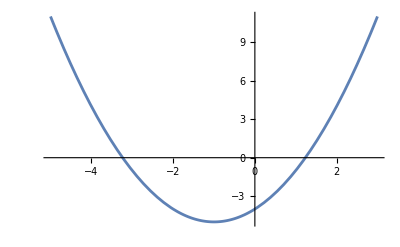

```mathematica
Plot[x^2 + 2 x - 4, {x, -5, 3}]
```

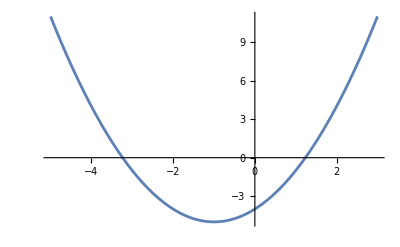

```mathematica
x = Subdivide[-5, 3, 100];
y = x^2 + 2 x - 4;
ListLinePlot[Transpose[{x, y}]]
```

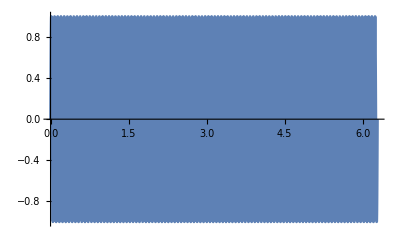

```mathematica
Plot[Sin[102 x], {x, 0, 2 Pi}, PlotPoints -> 100]
```

```mathematica
Plot3D[x^2 + y^2, {x, -1, 1}, {y, -1, 1}, AxesLabel -> {"x", "y"}]
```

-Graphics3D-

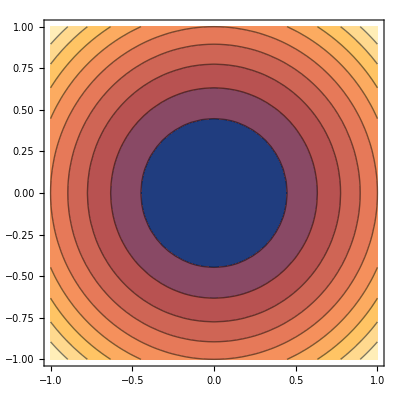

```mathematica
ContourPlot[x^2 + y^2, {x, -1, 1}, {y, -1, 1}]
```

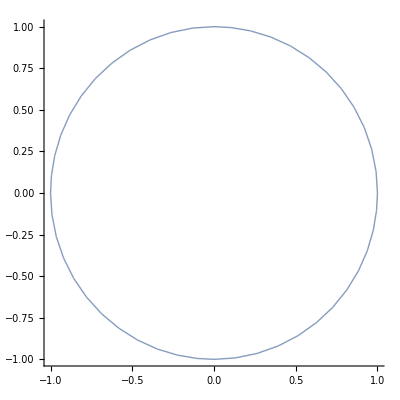

```mathematica
Clear[x, y];
reg1 = ImplicitRegion[x^2 + y^2 == 1, {x, y}];
Region[reg1, Axes -> True]
```

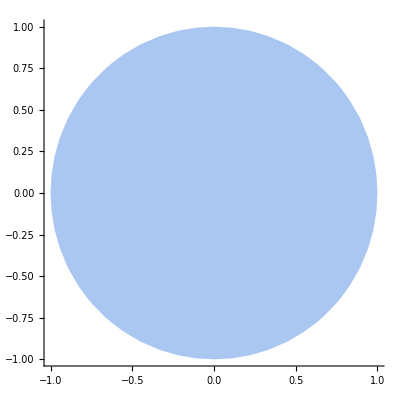

```mathematica
reg2 = ImplicitRegion[x^2 + y^2 <= 1, {x, y}];
Region[reg2, Axes -> True]
```

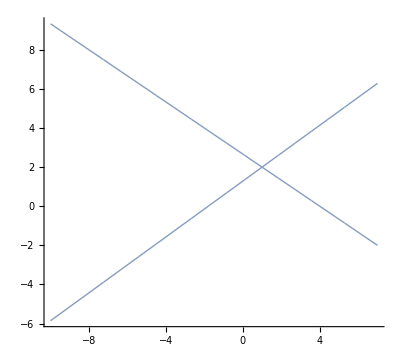

```mathematica
reg = ImplicitRegion[Or[2 x + 3 y == 8, 5 x - 7 y == -9], {x, y}];
Region[reg, Axes -> True]
```

-Graphics-

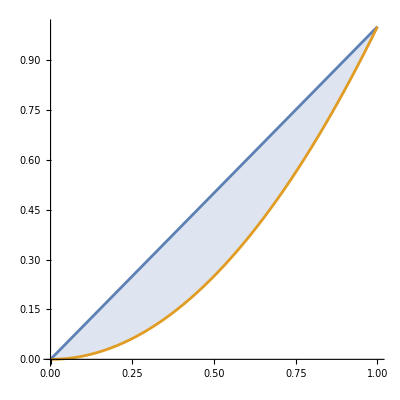

```mathematica
reg = ImplicitRegion[And[y <= x, y >= x^2], {x, y}];
RegionPlot[reg]                                                    (* ① *)
Plot[{x, x^2}, {x, 0, 1}, Filling -> {1 -> {2}}, AspectRatio -> 1] (* ② *)
```

```mathematica
{RegionMeasure[reg1], RegionMeasure[reg2]}
```

{2 π,π}

```mathematica
RegionMeasure[reg]
```

1/6

```mathematica
Clear[x];
{a, b} = Sort[SolveValues[{x == x^2}, x]];
Integrate[x - x^2, {x, a, b}]
```

1/6

```mathematica
Manipulate[
 ContourPlot[x^3 + y^3 - 3 x y == c, {x, -2, 2}, {y, -2, 2}],
 {{c, 0}, -1, 1}] (* cは-1以上1以下で，初期値は0 *)
```

```mathematica
Clear["Global`*"];
```

```mathematica
SolveValues[x^2 + 2 x - 4 == 0, x]
```

{-1-√5,-1+√5}

```mathematica
{a, b} = SolveValues[x^2 + 2 x - 4 == 0, x]
a + b

tmp = Solve[x^2 + 2 x - 4 == 0, x]
{a, b} = x /. tmp;
a + b

tmp = Reduce[x^2 + 2 x - 4 == 0, x]
{a, b} = x /. {ToRules[tmp]};
a + b
```

{-1-√5,-1+√5}

-2

{{x→-1-√5},{x→-1+√5}}

-2

x==-1-√5||x==-1+√5

-2

```mathematica
n = 3; Simplify[Total[SolveValues[x^n + 2 x - 4 == 0, x]]]
```

0

```mathematica
Clear["Global`*"];
```

```mathematica
sol = SolveValues[{2 x + 3 y == 8, 5 x - 7 y == -9}, {x, y}]
```

{{1,2}}

```mathematica
{{x1, y1}} = sol; x1 + y1
```

3

```mathematica
Clear["Global`*"];
```

```mathematica
f[x_] := 2^x + Sin[x]
FindRoot[f[x] == 0, {x, 0}]
```

{x→-0.676182}

```mathematica
Clear["Global`*"];
```

```mathematica
Reduce[x^2 + 2 x - 4 < 0, x]
```

-1-√5<x<-1+√5

## 5 論理式

```mathematica
Clear["Global`*"];
```

```mathematica
expr = Exists[x, Element[x, Reals], x^2 == 2];
Reduce[expr]
```

True

```mathematica
Reduce[Implies[x > 10, x > 11]]
```

x≤10||x>11

```mathematica
Reduce[ForAll[x, Element[x, Reals], Implies[x > 10, x > 11]]]
```

False

```mathematica
BooleanConvert[Implies[A, B], "OR"] (* 含意 *)
```

!A||B

```mathematica
BooleanConvert[And[A, B], "OR"] (* 論理積 *)
```

!(!A||!B)

```mathematica
{BooleanConvert[Not[A]] == BooleanConvert[Nand[A, A]],
 BooleanConvert[Or[A, B]] == BooleanConvert[Nand[Not[A], Not[B]]]}
```

{True,True}

```mathematica
Clear["Global`*"];
```

```mathematica
Reduce[Exists[x, Element[x, Reals], x^2 == 2]]
```

True

```mathematica
Reduce[Exists[x, x^2 == 2], Reals]
```

True

```mathematica
Reduce[Exists[x, Element[x, Rationals], x^2 == 2]] (* False *)
Reduce[Exists[x, x^2 == 2], Rationals]             (* False *)
```

False

False

```mathematica
Clear["Global`*"];
```

```mathematica
expr = ForAll[b, Element[b, Reals], Exists[n, Element[n, Integers], n > b]];
Reduce[expr]
```

True

```mathematica
expr1 = ForAll[b,
   Element[b, Reals], Exists[n, And[Element[n, Integers], n > b]]];
Reduce[expr1] (* True *)

expr2 = ForAll[b,
   Implies[Element[b, Reals], Exists[n, Element[n, Integers], n > b]]];
Reduce[expr2] (* 失敗 *)
```

True

Reduce::nsmet: -- Message text not found --

Reduce[∀_b(b∈ℝ⇒∃_(n,n∈ℤ)n>b)]

```mathematica
Clear["Global`*"];
```

```mathematica
Reduce[Exists[x, a x + b == 0]]
```

(b==0&&a==0)||a≠0

```mathematica
Reduce[Exists[x, Element[x, Reals], x^2 + a^2 == 0]]
```

Re[a]==0

```mathematica
Reduce[Exists[x, Element[x, Reals], x^2 + a^2 < 0]] (* False *)
```

False

```mathematica
Reduce[Exists[x, Element[x, Reals], x^2 + a^2 < 0], Complexes] // Simplify
```

Re[a]==0&&Im[a]≠0

```mathematica
Reduce[Not[Exists[{n, a, b, c}, And[n >= 3, a^n + b^n == c^n]]],
 PositiveIntegers]
```

True

```mathematica
Reduce[Not[Exists[{a, b, c}, a^4 + b^4 == c^4]], PositiveIntegers]
```

True

```mathematica
Reduce[Not[Exists[{a, b, c}, a^4 + b^4 == c^2]], PositiveIntegers] (* 失敗 *)
```

Reduce::nsmet: -- Message text not found --

Reduce[∀_{a,b,c}a^4+b^4≠c^2,]

## 6 1次元のデータ

```mathematica
Clear["Global`*"];
```

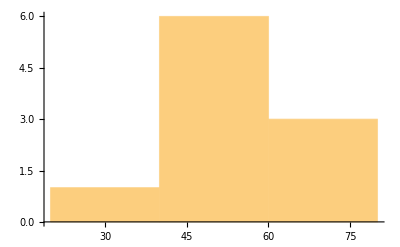

```mathematica
a = {36, 43, 53, 55, 56, 56, 57, 60, 61, 73};
b = {34, 39, 39, 49, 50, 52, 52, 55, 83, 97};
Histogram[a]
```

```mathematica
HistogramList[a, {20, 80, 20}]
```

{{20,40,60,80},{1,6,3}}

```mathematica
x = {7, 3, 1, 3, 4, 7, 7, 7, 10, 3};
f = Counts[x]
```

<|7→4,3→3,1→1,4→1,10→1|>

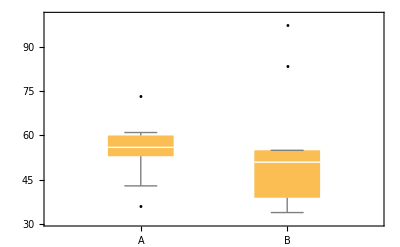

```mathematica
BoxWhiskerChart[{a, b}, "Outliers", ChartLabels -> {"A", "B"}]
```

```mathematica
Clear["Global`*"];
```

```mathematica
a = {36, 43, 53, 55, 56, 56, 57, 60, 61, 73};
Mean[a]
```

55

```mathematica
b = {34, 39, 39, 49, 50, 52, 52, 55, 83, 97};
Total[b]/Length[b]
```

55

```mathematica
Mean[a - Mean[a]]
```

0

```mathematica
Variance[a]
```

100

```mathematica
Total[(b - Mean[b])^2]/(Length[b] - 1) // N
```

397.778

```mathematica
z = Standardize[a]
```

{-19/10,-6/5,-1/5,0,1/10,1/10,1/5,1/2,3/5,9/5}

```mathematica
{Mean[z], StandardDeviation[z]}
```

{0,1}

```mathematica
(a - Mean[a])/StandardDeviation[a]
```

{-19/10,-6/5,-1/5,0,1/10,1/10,1/5,1/2,3/5,9/5}

```mathematica
StandardDeviation[a] z + Mean[a]
```

{36,43,53,55,56,56,57,60,61,73}

```mathematica
10 * z + 50
```

{31,38,48,50,51,51,52,55,56,68}

## 7 2次元のデータ

```mathematica
Clear["Global`*"];
```

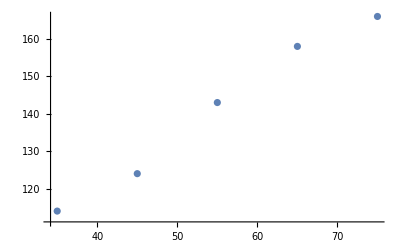

```mathematica
x = {35, 45, 55, 65, 75}; y = {114, 124, 143, 158, 166};
ListPlot[Transpose[{x, y}]]
```

```mathematica
Clear["Global`*"];
```

```mathematica
x = {35, 45, 55, 65, 75}; y = {114, 124, 143, 158, 166};
Covariance[x, y]
```

345

```mathematica
Covariance[Transpose[{x, y}]]
```

{{250,345},{345,484}}

```mathematica
(x - Mean[x]) . (y - Mean[y])/(Length[x] - 1)
```

345

```mathematica
Correlation[x, y] // N
```

0.991805

```mathematica
Clear["Global`*"];
```

```mathematica
x = {35, 45, 55, 65, 75}; y = {114, 124, 143, 158, 166};
data = Thread[{x, y}]; (* x, yを列とする行列 *)
model = LinearModelFit[data, X, X]
```

FittedModel[…]

```mathematica
model[40]
```

120.3

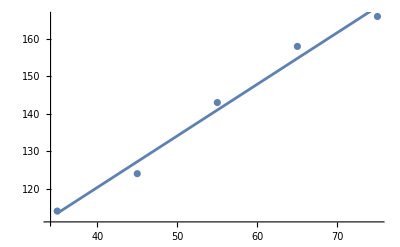

```mathematica
Show[ListPlot[data], Plot[model[x], {x, 35, 75}]]
```

```mathematica
L = Total[(y - (a x + b))^2]
```

(166-75 a-b)^2+(158-65 a-b)^2+(143-55 a-b)^2+(124-45 a-b)^2+(114-35 a-b)^2

```mathematica
sol = SolveAlways[L == p (a - q)^2 + r (b - (s a + t))^2 + u, {a, b}]
{q, s q + t} /. sol[[1]]
```

{{u→158/5,p→1000,q→69/50,s→-55,t→141,r→5}}

{69/50,651/10}

```mathematica
a = Covariance[x, y]/Variance[x]; b = Mean[y] - a Mean[x];
{a, b} // N
```

{1.38,65.1}

```mathematica
Clear["Global`*"];
```

0.816421

FittedModel[…]

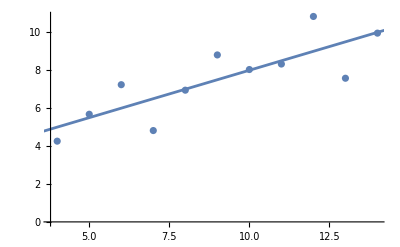

```mathematica
anscombe = ExampleData[{"Statistics", "AnscombeRegressionLines"}];
x1 = anscombe[[All, 1]]; y1 = anscombe[[All, 5]]; data = Thread[{x1, y1}];
Correlation[x1, y1]
model = LinearModelFit[data, X, X]
Show[ListPlot[data], Plot[model[x], {x, 0, 21}]]
```

## 8 確率変数と確率分布

```mathematica
Clear["Global`*"];
```

```mathematica
dist = DiscreteUniformDistribution[{1, 6}];
PDF[dist][2]
```

1/6

```mathematica
Probability[X == 2, Distributed[X, dist]]
```

1/6

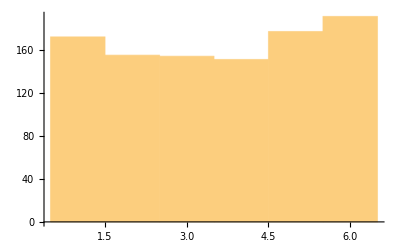

```mathematica
data = RandomVariate[dist, 1000];
Histogram[data] (* 結果は割愛 *)
```

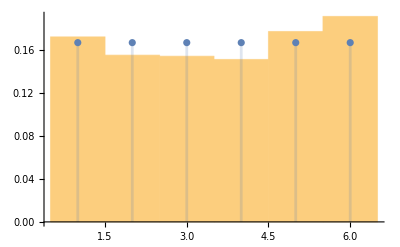

```mathematica
Show[Histogram[data, {0.5, 6.5, 1}, "PDF"],
 DiscretePlot[PDF[dist][x], {x, 1, 6}]]
```

```mathematica
dist = BernoulliDistribution[3/10];
data = RandomVariate[dist, 1000];
Counts[data]
```

<|0→711,1→289|>

```mathematica
dist = BinomialDistribution[10, 3/10];
PDF[dist][3]
```

66706983/250000000

```mathematica
Probability[X == 3, Distributed[X, dist]]
```

66706983/250000000

```mathematica
dist = BinomialDistribution[n, p];
PDF[dist]
```

Function[x,Piecewise[{{(1-p)^(-x+n) p^x Binomial[n,x], 0≤x≤n}, {0, True}}],Listable]

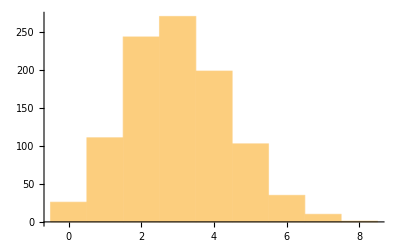

```mathematica
n = 10; p = 3/10; dist = BinomialDistribution[n, p];
data = RandomVariate[dist, 1000];
Histogram[data] (* 結果は割愛 *)
```

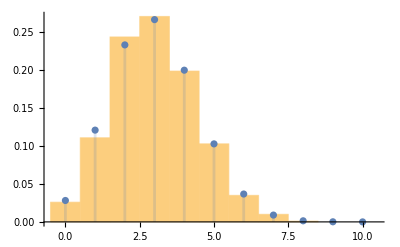

```mathematica
Show[Histogram[data, {-0.5, n + 0.5, 1}, "PDF"],
 DiscretePlot[PDF[dist][x], {x, 0, n}]]
```

```mathematica
dist = BinomialDistribution[10, 3/10];
CDF[dist][3]
```

406006699/625000000

```mathematica
Probability[X <= 3, Distributed[X, dist]]
```

406006699/625000000

```mathematica
Sum[PDF[dist][k], {k, 0, 3}]
```

406006699/625000000

```mathematica
Clear["Global`*"];
```

```mathematica
dist = UniformDistribution[{0, 360}];
{CDF[dist][200], CDF[dist][150], CDF[dist][200] - CDF[dist][150]}
```

{5/9,5/12,5/36}

```mathematica
Probability[150 <= X <= 200, Distributed[X, dist]]
```

5/36

```mathematica
Integrate[PDF[dist][x], {x, 150, 200}]
```

5/36

```mathematica
Integrate[PDF[dist][t], {t, 0, x},
 Assumptions -> Element[x, Reals]] (* xは実数と仮定する．*)
```

Piecewise[{{1, x>360}, {x/360, 0<x≤360}, {0, True}}]

```mathematica
D[x/360, x]
```

1/360

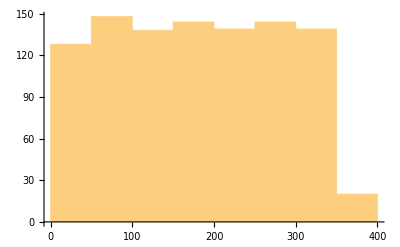

```mathematica
data = RandomVariate[dist, 1000];
Histogram[data] (* 結果は割愛 *)
```

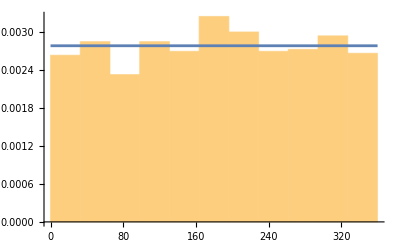

```mathematica
data = RandomVariate[dist, 1000];
Show[Histogram[data, {"Raw", "Sturges"}, "PDF"],
 Plot[PDF[dist][x], {x, 0, 360}]]
```

```mathematica
dist = NormalDistribution[6, 2];
CDF[dist][6 + 3 2] - CDF[dist][6 - 3 2] // N
```

0.9973

```mathematica
Probability[6 - 3 2 <= X <= 6 + 3 2, Distributed[X, dist]] // N
```

0.9973

```mathematica
Integrate[PDF[dist][x], {x, 6 - 3 2, 6 + 3 2}] // N
```

0.9973

```mathematica
Clear[mu, sigma, x];
dist = NormalDistribution[mu, sigma];
{a, b} = {mu - 3 sigma, mu + 3 sigma};
CDF[dist][b] - CDF[dist][a] // N                    (* 方法1 *)
Probability[a <= X <= b, Distributed[X, dist]] // N (* 方法2 *)
Integrate[PDF[dist][x], {x, a, b}] // N             (* 方法3 *)
```

0.9973

0.9973

0.9973

```mathematica
dist = NormalDistribution[mu, sigma];
PDF[dist][x]
```

(ⅇ^(-(-mu+x)^2/(2 sigma^2)))/(√(2 π) sigma)

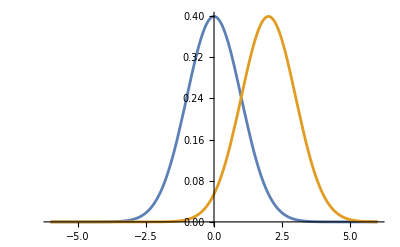

```mathematica
Plot[{PDF[NormalDistribution[0, 1]][x],
      PDF[NormalDistribution[2, 1]][x]}, {x, -6, 6}]
```

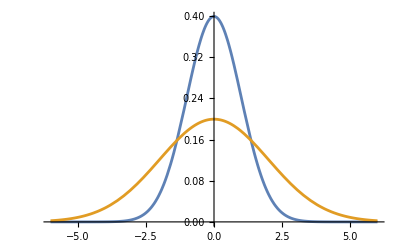

```mathematica
Plot[{PDF[NormalDistribution[0, 1]][x],
      PDF[NormalDistribution[0, 2]][x]}, {x, -6, 6}]
```

```mathematica
Clear["Global`*"];
```

```mathematica
Xs = {0, 100, 1000, 10000}; Ps = {0.9, 0.08, 0.015, 0.005};
tmp = Piecewise[Thread[{Ps, Thread[x == Xs]}]];
dist = ProbabilityDistribution[tmp, {x, 0, 10000, 1}, (* 確率分布の定義 *)
   Method -> "Normalize"]; (* 念のため合計を1にする．*)
data = RandomVariate[dist, 1000];
Counts[data]
```

<|0→909,100→71,1000→14,10000→6|>

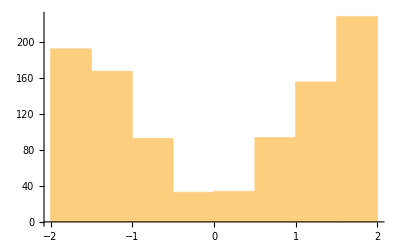

```mathematica
dist = ProbabilityDistribution[Abs[x], {x, -2, 2}, (* 確率分布の定義 *)
   Method -> "Normalize"]; (*“全確率”が1にならない場合の備え *)
data = RandomVariate[dist, 1000];
Histogram[data]
```

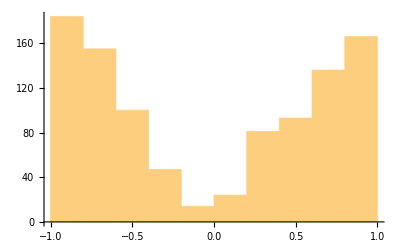

```mathematica
Clear[f, F, t, x];
f[x_] := RealAbs[x]                            (* 手順1 *)
F[x_] := Evaluate[Integrate[f[t], {t, -1, x}]] (* 手順2 *)
Finv = InverseFunction[F];                     (* 手順3 *)
data = Table[Finv[RandomReal[]], {1000}];      (* 手順4 *)
Histogram[data]                                (* 手順5 *)
```

```mathematica
distY = UniformDistribution[{0, 1}];
distX = TransformedDistribution[
   Piecewise[{{-Sqrt[1 - 2 Y], Y <= 1/2}}, Sqrt[-1 + 2 Y]],
   Distributed[Y, distY]];
PDF[distX]
```

Function[x,Piecewise[{{-x, -1<x≤0}, {x, 0<x≤1}, {0, True}}],Listable]

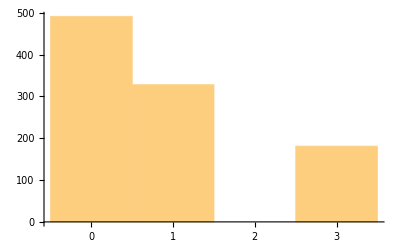

```mathematica
distX = DiscreteUniformDistribution[{1, 6}];
distY = TransformedDistribution[Mod[X^3, 4], Distributed[X, distX]];
data = RandomVariate[distY, 1000];
Histogram[data]
```

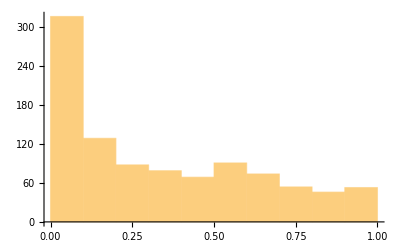

```mathematica
distX = UniformDistribution[{0, 1}];
distY = TransformedDistribution[X^2, Distributed[X, distX]];
data = RandomVariate[distY, 1000];
Histogram[data]
```

```mathematica
PDF[distY]
```

Function[x,Piecewise[{{1/(2 √x), 0<x<1}, {0, True}}],Listable]

```mathematica
distX = ProbabilityDistribution[Abs[x], {x, -1, 1}];
distY = TransformedDistribution[X^2, Distributed[X, distX]];
PDF[distY]
```

Function[x,Piecewise[{{1, 0<x<1}, {0, x>1||x<0}, {Indeterminate, True}}],Listable]

```mathematica
dist = NormalDistribution[mu, sigma]; Clear[a, b];
TransformedDistribution[a X + b, Distributed[X, dist]]
```

NormalDistribution[b+a mu,sigma Abs[a]]

```mathematica
Clear["Global`*"];
```

```mathematica
Xs = {0, 100, 1000, 10000}; Ps = {0.9, 0.08, 0.015, 0.005};
tmp = Piecewise[Thread[{Ps, Thread[x == Xs]}]];
dist = ProbabilityDistribution[tmp, {x, 0, 10000, 1}];
Expectation[X, Distributed[X, dist]]
```

73.

```mathematica
Mean[dist]
```

73.

```mathematica
Sum[x PDF[dist][x], {x, Xs}]
```

73.

```mathematica
Xs . Ps
```

73.

```mathematica
Mean[RandomVariate[dist, 500000]] // N
```

72.1082

```mathematica
Clear[n, p];
dist = BinomialDistribution[n, p];
Expectation[X, Distributed[X, dist]]       (* 方法1 *)
Mean[dist]                                 (* 方法2 *)
Sum[x PDF[dist][x], {x, 0, n}] // Simplify (* 方法3 *)
```

n p

n p

Piecewise[{{n p, n≥1}, {0, True}}]

```mathematica
dist = ProbabilityDistribution[Abs[x], {x, -1, 1}];
Integrate[x PDF[dist][x], {x, -1, 1}]
```

0

```mathematica
Xs = {0, 100, 1000, 10000}; Ps = {0.9, 0.08, 0.015, 0.005};
tmp = Piecewise[Thread[{Ps, Thread[x == Xs]}]];
dist = ProbabilityDistribution[tmp, {x, 0, 10000, 1}];
Variance[dist]
```

510471.

```mathematica
Expectation[(X - Mean[dist])^2, Distributed[X, dist]]
```

510471.

```mathematica
Sum[(x - Mean[dist])^2 PDF[dist][x], {x, Xs}]
```

510471.

```mathematica
((Xs - Xs . Ps)^2) . Ps
```

510471.

```mathematica
Clear[n, p];
dist = BinomialDistribution[n, p];
Variance[dist]                                              (* 方法1 *)
Expectation[(X - Mean[dist])^2, Distributed[X, dist]]       (* 方法2 *)
Sum[(x - Mean[dist])^2 PDF[dist][x], {x, 0, n}] // Simplify (* 方法3 *)
```

n (1-p) p

n p-n p^2

-n (-1+p) p

```mathematica
dist = ProbabilityDistribution[Abs[x], {x, -1, 1}];
Integrate[(x - Mean[dist])^2 PDF[dist][x], {x, -1, 1}]
```

1/2

## 9 多次元の確率分布

```mathematica
Clear["Global`*"];
```

```mathematica
distX = DiscreteUniformDistribution[{1, 6}];
dist = TransformedDistribution[{Max[X1, X2], Min[X1, X2]},
   {Distributed[X1, distX], Distributed[X2, distX]}];
probs = Table[{
   Probability[{X, Y} == {x, y}, Distributed[{X, Y}, dist]], (* 確率 *)
   {X, Y} == {x, y}},                                        (* 条件 *)
  {x, 1, 6}, {y, 1, 6}]

dist = ProbabilityDistribution[Piecewise[Flatten[probs, 1]], (* 作り直し *)
   {X, 1, 6, 1}, {Y, 1, 6, 1}];
```

{{{1/36,{X,Y}=={1,1}},{0,{X,Y}=={1,2}},{0,{X,Y}=={1,3}},{0,{X,Y}=={1,4}},{0,{X,Y}=={1,5}},{0,{X,Y}=={1,6}}},{{1/18,{X,Y}=={2,1}},{1/36,{X,Y}=={2,2}},{0,{X,Y}=={2,3}},{0,{X,Y}=={2,4}},{0,{X,Y}=={2,5}},{0,{X,Y}=={2,6}}},{{1/18,{X,Y}=={3,1}},{1/18,{X,Y}=={3,2}},{1/36,{X,Y}=={3,3}},{0,{X,Y}=={3,4}},{0,{X,Y}=={3,5}},{0,{X,Y}=={3,6}}},{{1/18,{X,Y}=={4,1}},{1/18,{X,Y}=={4,2}},{1/18,{X,Y}=={4,3}},{1/36,{X,Y}=={4,4}},{0,{X,Y}=={4,5}},{0,{X,Y}=={4,6}}},{{1/18,{X,Y}=={5,1}},{1/18,{X,Y}=={5,2}},{1/18,{X,Y}=={5,3}},{1/18,{X,Y}=={5,4}},{1/36,{X,Y}=={5,5}},{0,{X,Y}=={5,6}}},{{1/18,{X,Y}=={6,1}},{1/18,{X,Y}=={6,2}},{1/18,{X,Y}=={6,3}},{1/18,{X,Y}=={6,4}},{1/18,{X,Y}=={6,5}},{1/36,{X,Y}=={6,6}}}}

```mathematica
PDF[MarginalDistribution[dist, 1]][x] // Simplify
PDF[MarginalDistribution[dist, 2]][y] // Simplify
```

Piecewise[{{1/36, x==1}, {1/12, x==2}, {5/36, x==3}, {7/36, x==4}, {1/4, x==5}, {11/36, x==6}, {0, True}}]

Piecewise[{{11/36, y==1}, {1/4, y==2}, {7/36, y==3}, {5/36, y==4}, {1/12, y==5}, {1/36, y==6}, {0, True}}]

```mathematica
Table[CDF[dist][{x, y}], {y, 1, 6}, {x, 1, 6}] // TableForm
```

1/36 | 1/12 | 5/36 | 7/36 | 1/4 | 11/36
1/36 | 1/9 | 2/9 | 1/3 | 4/9 | 5/9
1/36 | 1/9 | 1/4 | 5/12 | 7/12 | 3/4
1/36 | 1/9 | 1/4 | 4/9 | 2/3 | 8/9
1/36 | 1/9 | 1/4 | 4/9 | 25/36 | 35/36
1/36 | 1/9 | 1/4 | 4/9 | 25/36 | 1

```mathematica
Clear["Global`*"];
```

```mathematica
c = Counts[Flatten[Table[{Max[x, y], Min[x, y]}, {x, 1, 6}, {y, 1, 6}], 1]]/36;
dist = ProbabilityDistribution[Piecewise[KeyValueMap[{#2, {X, Y} == #1} &, c]],
   {X, 1, 6, 1}, {Y, 1, 6, 1}];

Mean[dist]                (* 平均 *)
Variance[dist]            (* 分散 *)
StandardDeviation[dist]   (* 標準偏差 *)
Covariance[dist][[1, 2]]  (* 共分散 *)
Correlation[dist][[1, 2]] (* 相関係数 *)
```

{161/36,91/36}

{2555/1296,2555/1296}

{(√2555)/36,(√2555)/36}

1225/1296

35/73

```mathematica
{uX, uY} = Mean[dist]; {sX, sY} = StandardDeviation[dist];
Expectation[{X, Y,           (* 平均 *)
   (X - uX)^2, (Y - uY)^2,   (* 分散 *)
   (X - uX) (Y - uY),        (* 共分散 *)
   (X - uX) (Y - uY)/sX/sY}, (* 相関係数 *)
  Distributed[{X, Y}, dist]]
```

{161/36,91/36,2555/1296,2555/1296,1225/1296,35/73}

```mathematica
Sum[x Probability[X == x, Distributed[{X, Y}, dist]], {x, 1, 6}] (* 平均 *)
Sum[(x - uX) (y - uY) PDF[dist][{x, y}], {x, 1, 6}, {y, 1, 6}]   (* 共分散 *)
```

161/36

1225/1296

```mathematica
Clear["Global`*"];
```

```mathematica
dist = DiscreteUniformDistribution[{1, 6}];
Probability[Conditioned[X == 2, X <= 3], Distributed[X, dist]]
```

1/3

```mathematica
c = Counts[Flatten[Table[{Max[x, y], Min[x, y]}, {x, 1, 6}, {y, 1, 6}], 1]]/36;
dist = ProbabilityDistribution[Piecewise[KeyValueMap[{#2, {X, Y} == #1} &, c]],
   {X, 1, 6, 1}, {Y, 1, 6, 1}];
rule = Distributed[{X, Y}, dist];

Table[Probability[Conditioned[X == x, Y == 3], rule], {x, 1, 6}]
```

{0,0,1/7,2/7,2/7,2/7}

```mathematica
Table[
 Probability[And[X == x, Y == 3], rule]/Probability[Y == 3, rule], {x, 1, 6}]
```

{0,0,1/7,2/7,2/7,2/7}

```mathematica
Expectation[Conditioned[X, Y == 3], rule]
```

33/7

```mathematica
Sum[x Probability[Conditioned[X == x, Y == 3], rule], {x, 1, 6}]
```

33/7

```mathematica
Table[Probability[And[X <= x, Y <= y], rule], {x, 1, 6}, {y, 1, 6}] ==
  Table[Probability[X <= x, rule] Probability[Y <= y, rule],
  {x, 1, 6}, {y, 1, 6}]
```

False

```mathematica
distU = DiscreteUniformDistribution[{1, 6}];
distXY = TransformedDistribution[{Mod[U, 2], Mod[U, 3]},
   Distributed[U, distU]];
rule = Distributed[{X, Y}, distXY];
Table[Probability[And[X <= x, Y <= y], rule], {x, 0, 1}, {y, 0, 2}] ==
 Table[Probability[X <= x, rule] Probability[Y <= y, rule],
  {x, 0, 1}, {y, 0, 2}]
```

True

```mathematica
distX = BinomialDistribution[3, 1/2];
distXY = TransformedDistribution[
   {X, Piecewise[{{1, Or[X == 0, X == 3]}}, 2]}, Distributed[X, distX]];
Covariance[distXY][[1, 2]]
```

0

```mathematica
rule = Distributed[{X, Y}, distXY];
Table[Probability[And[X <= x, Y <= y], rule], {x, 0, 3}, {y, 1, 2}] ==
 Table[Probability[X <= x, rule] Probability[Y <= y, rule],
  {x, 0, 3}, {y, 1, 2}]
```

False

```mathematica
Clear["Global`*"];
```

```mathematica
c = Counts[Flatten[Table[{Max[x, y], Min[x, y]}, {x, 1, 6}, {y, 1, 6}], 1]]/36;
dist = ProbabilityDistribution[Piecewise[KeyValueMap[{#2, {X, Y} == #1} &, c]],
   {X, 1, 6, 1}, {Y, 1, 6, 1}];
rule = Distributed[{X, Y}, dist];

{Expectation[X + Y, rule],
 Expectation[X, rule] + Expectation[Y, rule]} (* 平均1 *)

{distX, distY} = Table[MarginalDistribution[dist, i], {i, 2}];
distXplusY = TransformedDistribution[X + Y, rule];

{Mean[distXplusY], Mean[distX] + Mean[distY]} (* 平均2 *)
{Variance[distXplusY],
 Variance[distX] + Variance[distY] + 2 Covariance[dist][[1, 2]]} (* 分散 *)
```

{7,7}

{7,7}

{35/6,35/6}

```mathematica
Manipulate[
 distY = BinomialDistribution[n, p];
 mu = Mean[distY]; sigma = StandardDeviation[distY];
 distZ = NormalDistribution[mu, sigma];
 Show[DiscretePlot[PDF[distY][x], {x, 0, n}], Plot[PDF[distZ][x], {x, 0, n}]],
 {{n, 15}, 1, 40, 1}, {{p, 4/10}, 0, 1}]
```

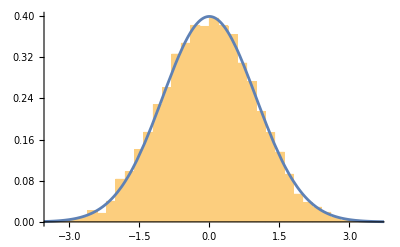

```mathematica
distX = UniformDistribution[]; distZ = NormalDistribution[];
data = Table[Total[RandomVariate[distX, 12]] - 6, {10000}];
Show[Histogram[data, Automatic, "PDF"], Plot[PDF[distZ][x], {x, -4, 4}]]
```

```mathematica
Clear["Global`*"];
```

```mathematica
dist1 = NormalDistribution[0, 2]; dist2 = NormalDistribution[1, 1];
TransformedDistribution[{X1 + X2 + 2, X1 + 3 X2 + 3},
 {Distributed[X1, dist1], Distributed[X2, dist2]}]
```

MultinormalDistribution[{3,6},{{5,7},{7,13}}]

```mathematica
mu = {3, 6}; Sigma = {{5, 7}, {7, 13}};
dist = MultinormalDistribution[mu, Sigma];
Plot3D[PDF[dist][{Y1, Y2}], {Y1, -8, 14}, {Y2, -5, 17},
 PlotPoints -> 100, PlotRange -> All, AxesLabel -> Automatic]
```

-Graphics3D-

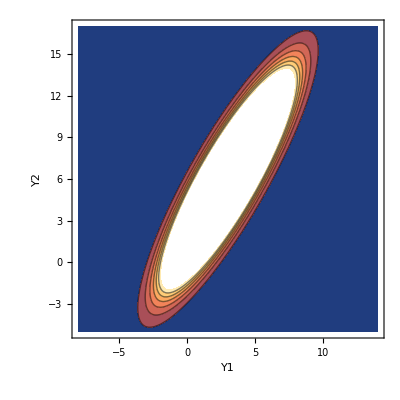

```mathematica
ContourPlot[PDF[dist][{Y1, Y2}], {Y1, -8, 14}, {Y2, -5, 17},
 PlotPoints -> 50, FrameLabel -> Automatic]
```

```mathematica
sol = Solve[{Y1 == X1 + X2 + 2, Y2 == X1 + 3 X2 + 3}, {X1, X2}][[1]]
```

{X1→1/2 (-3+3 Y1-Y2),X2→1/2 (-1-Y1+Y2)}

```mathematica
J = D[{X1, X2} /. sol, {{Y1, Y2}}];
absj = Abs[Det[J]]
```

1/2

```mathematica
f1 = PDF[dist1]; f2 = PDF[dist2];
PDF[dist][{Y1, Y2}] == f1[X1] f2[X2] absj /. sol // Simplify
```

True

```mathematica
{MarginalDistribution[dist, 1], MarginalDistribution[dist, 2]}
```

{NormalDistribution[3,√5],NormalDistribution[6,√13]}

```mathematica
dist = MultinormalDistribution[{u1, u2}, {{v1, 0}, {0, v2}}];
d1 = MarginalDistribution[dist, 1]; d2 = MarginalDistribution[dist, 2];
Simplify[CDF[dist][{x1, x2}] == CDF[d1][x1] CDF[d2][x2],
 And[v1 >= 0, v2 >= 0]]
```

True

## 10 推測統計

```mathematica
Clear["Global`*"];
```

```mathematica
dist = NormalDistribution[2, 3];
data1 = Table[Mean[RandomVariate[dist, 5]], 10000];
data2 = Table[Mean[RandomVariate[dist, 50]], 10000];
{{Mean[data1], Variance[data1]}, {Mean[data2], Variance[data2]}}
```

{{2.01413,1.83253},{1.99802,0.182192}}

```mathematica
Histogram[{data1, data2}, ChartLayout -> "Row"]
```

-Graphics-

```mathematica
dist = NormalDistribution[2, 3];
data1 = Table[Variance[RandomVariate[dist, 5]], 10000];
data2 = Table[Variance[RandomVariate[dist, 50]], 10000];
{{Mean[data1], Variance[data1]}, {Mean[data2], Variance[data2]}}
```

{{9.05559,40.3025},{9.00464,3.26093}}

```mathematica
Histogram[{data1, data2}, ChartLayout -> "Row"]
```

-Graphics-

```mathematica
Clear["Global`*"];
```

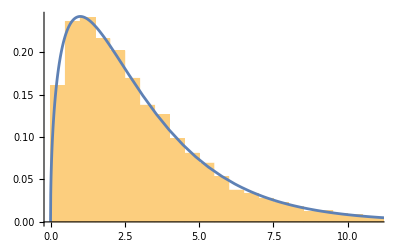

```mathematica
n = 4; mu = 5; sigma = 7; dist := NormalDistribution[mu, sigma];
f[x_] := (n - 1) Variance[x]/sigma^2
data = Table[f[RandomVariate[dist, n]], 10000];
Show[Histogram[data, Automatic, "PDF"],
 Plot[PDF[ChiSquareDistribution[n - 1]][x], {x, 0, Max[data]}]]
```

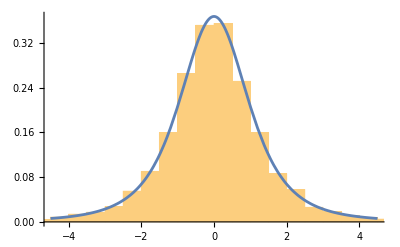

```mathematica
n = 4; mu = 5; sigma = 7; ndist = NormalDistribution[mu, sigma];
t = Function[{x}, (Mean[x] - mu)/Sqrt[Variance[x]/n]];
data = Table[t[RandomVariate[ndist, n]], 10000];
Show[Histogram[data, Automatic, "PDF"],
 Plot[PDF[StudentTDistribution[n - 1]][x], {x, -4.5, 4.5}]]
```

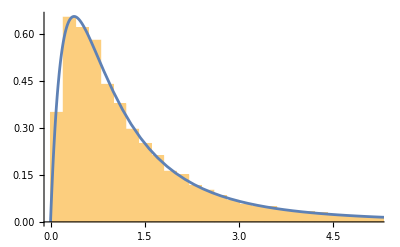

```mathematica
m = 5; muX = 2; sigmaX = 3; distX = NormalDistribution[muX, sigmaX];
n = 7; muY = 3; sigmaY = 2; distY = NormalDistribution[muY, sigmaY];
f[x_, y_] := (Variance[x]/sigmaX^2)/(Variance[y]/sigmaY^2)
data = Table[f[RandomVariate[distX, m], RandomVariate[distY, n]], {10000}];
Show[Histogram[data, Automatic, "PDF"],
 Plot[PDF[FRatioDistribution[m - 1, n - 1]][x], {x, 0, 7}]]
```

```mathematica
Clear[k, T];
TransformedDistribution[T^2, Distributed[T, StudentTDistribution[k]]]
```

FRatioDistribution[1,k]

```mathematica
Clear["Global`*"];
```

```mathematica
n = 15; p0 = 4/10; dist = BinomialDistribution[n, p0];
tmp = Table[PDF[dist][x], {x, 0, n}];
Total[Cases[tmp, p_ /; p <= PDF[dist][2]]] // N
```

0.0364617

```mathematica
CDF[dist][2] // N
```

0.027114

```mathematica
n = 15; p0 = 4/10; dist = NormalDistribution[n p, Sqrt[n p (1 - p)]];
2 CDF[dist /. p -> p0][2] // N
```

0.035015

```mathematica
alpha = 5/100; InverseCDF[dist /. {p -> p0}, {alpha/2, 1 - alpha/2}] // N
```

{2.28123,9.71877}

```mathematica
N[Reduce[InverseCDF[dist, alpha/2] <= 2 <= InverseCDF[dist, 1 - alpha/2], p]]
```

0.0373613≤p≤0.37882

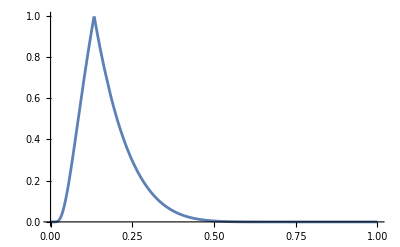

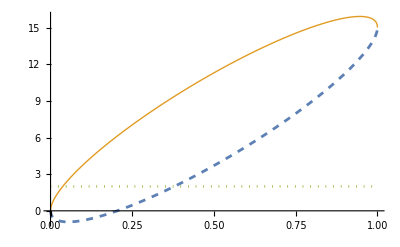

```mathematica
pvalue[p0_] := With[{c = CDF[dist][2] /. p -> p0}, 2 Min[c, 1 - c]]
Plot[pvalue[p0], {p0, 0, 1}]

Plot[{InverseCDF[dist, alpha/2], InverseCDF[dist, 1 - alpha/2], 2},
 {p, 0, 1}, PlotStyle -> {Dashed, Thick, Dotted}]
```

```mathematica
Clear["Global`*"];
```

```mathematica
x = {24.2, 25.3, 26.2, 25.7, 24.4, 25.1, 25.6}; mu0 = 25;
TTest[x, mu0]
```

0.458101

```mathematica
m = Mean[x]; s2 = Variance[x]; n = Length[x];
t := (m - mu0)/Sqrt[s2/n];
dist = StudentTDistribution[n - 1]; c = CDF[dist][t];
2 Min[c, 1 - c]
```

0.458101

```mathematica
alpha = 5/100;
{a, b} = InverseCDF[dist, {alpha/2, 1 - alpha/2}] // N
```

{-2.44691,2.44691}

```mathematica
Needs["HypothesisTesting`"] (*「`」はシングルクォートではなくバッククォート *)
MeanCI[x]
```

{24.5529,25.8757}

```mathematica
Clear[mu0]; Reduce[a <= t <= b, mu0]
```

Reduce::ratnz: -- Message text not found --

24.5529≤mu0≤25.8757

```mathematica
dist = StudentTDistribution[n - 1];
Reduce[InverseCDF[dist, alpha/2] <= t <= InverseCDF[dist, 1 - alpha/2]]
```

Reduce::ratnz: -- Message text not found --

24.5529≤mu0≤25.8757

```mathematica
x = {25, 24, 25, 26}; y = {23, 18, 22, 28, 17, 25, 19, 16};
TTest[{x, y}, 0, AlternativeHypothesis -> "Greater",
 VerifyTestAssumptions -> "EqualVariance" -> False]
```

0.0160194

```mathematica
alpha = 5/100;
m = Length[x]; n = Length[y]; sx2 = Variance[x]; sy2 = Variance[y];
s2 = ((m - 1) sx2 + (n - 1) sy2)/(m + n - 2);
T = (Mean[x] - Mean[y] - d)/Sqrt[s2 (1/m + 1/n)]; (* t統計量 *)
t := T /. d -> 0                                  (* t値 *)
df = m + n - 2;                                   (* 自由度 *)
dist := StudentTDistribution[df];                 (* t分布 *)
P := 1 - CDF[dist][t];                            (* P値 *)
a := InverseCDF[dist, 1 - alpha];                 (* 採択域の上限 *)
interval := Reduce[T <= a, d]                     (* 信頼区間 *)
{t, P, a, interval} // N
```

{1.84017,0.0477856,1.81246,d≥0.0602415}

```mathematica
T = (Mean[x] - Mean[y] - d)/Sqrt[sx2/m + sy2/n];
df = (sx2/m + sy2/n)^2/((sx2/m)^2/(m - 1) + (sy2/n)^2/(n - 1)) // N;
{t, P, a, interval} // N
```

Reduce::ratnz: -- Message text not found --

{2.5923,0.0160194,1.85992,d≥1.13009}

```mathematica
x = {25, 24, 25, 26}; y = {23, 18, 22, 28, 17, 25, 19, 16};
VarianceTest[{x, y}, 1, "HypothesisTestData"]["TestDataTable"]
```

| Statistic | P-Value
Fisher Ratio | 0.0376344 | 0.021215

```mathematica
m = Length[x]; n = Length[y]; dist = FRatioDistribution[m - 1, n - 1];
F = Variance[x]/Variance[y]/r; f = F /. r -> 1;
c = CDF[dist][f];
{f, 2 Min[c, 1 - c]} // N
```

{0.0376344,0.021215}

```mathematica
alpha = 5/100;
{a, b} = InverseCDF[dist, {alpha/2, 1 - alpha/2}] // N
```

{0.0683789,5.88982}

```mathematica
Needs["HypothesisTesting`"] (*「`」はシングルクォートではなくバッククォート *)
VarianceRatioCI[x, y]
```

{0.00638974,0.55038}

```mathematica
Reduce[a <= F <= b, r]
```

Reduce::ratnz: -- Message text not found --

0.00638974≤r≤0.55038

## 11 線形回帰分析

```mathematica
Clear["Global`*"];
```

```mathematica
data = {{1, 2, 3}, {1, 3, 6}, {2, 5, 3}, {3, 7, 6}};
model = LinearModelFit[data, {X1, X2}, {X1, X2}]
model["BestFitParameters"]
```

FittedModel[…]

{3.,-4.,2.}

```mathematica
model[1.5, 4]
```

5.

```mathematica
x1 = {1, 3, 6, 10}; y = {7, 1, 6, 14};
e = y - (b0 + b1 x1);
L = e . e; (* 内積 *)
FindMinimum[L, {{b0, 0}, {b1, 0}}]
```

{40.,{b0→2.,b1→1.}}

```mathematica
Minimize[L, {b0, b1}] (* 解析的な結果 *)
```

{40,{b0→2,b1→1}}

```mathematica
L = Total[Abs[e]]; (* 差の絶対値の和 *)
Minimize[L, {b0, b1}] // N
```

{10.2857,{b0→-4.57143,b1→1.85714}}

```mathematica
e = x1 - (y - b0)/b1;
L = e . e;
Minimize[L, {b0, b1}] // N
```

{21.3953,{b0→-2.34783,b1→1.86957}}

```mathematica
line = Module[{x1, y}, ImplicitRegion[y == b0 + b1 x1, {x1, y}]];
L = Sum[RegionDistance[line, p]^2, {p, Thread[{x1, y}]}];
Minimize[L, {b0, b1}] // Simplify // N
```

{15.8403,{b0→-0.626059,b1→1.52521}}

```mathematica
data = {{1, 2, 3}, {1, 3, 6}, {2, 5, 3}, {3, 7, 6}};
X = DesignMatrix[data, {X1, X2}, {X1, X2}];
y = data[[All, -1]];
Inverse[Transpose[X] . X] . Transpose[X] . y
```

{3,-4,2}

```mathematica
PseudoInverse[X] . y
```

{3,-4,2}

```mathematica
b = {b0, b1, b2};
L = (y - X . b) . (y - X . b);
Reduce[{D[L, {b}] == 0 b}]
```

b2==2&&b1==-4&&b0==3

```mathematica
D[L, {b}] == -2 Transpose[X] . y + 2 Transpose[X] . X . b // Simplify
```

True

```mathematica
Clear["Global`*"];
```

```mathematica
data = {{1, 2, 3}, {1, 3, 6}, {2, 5, 3}, {3, 7, 6}};
model = LinearModelFit[data, {X1, X2}, {X1, X2}];
model["RSquared"]
```

0.333333

```mathematica
model["AdjustedRSquared"]
```

-1.

```mathematica
x1 = {1, 3, 6, 10}; y = {7, 1, 6, 14}; data = Thread[{x1, y}];
X = DesignMatrix[data, X1, X1];
yh = X . PseudoInverse[X] . y;
eh = y - yh; fh = yh - Mean[y]; g = y - Mean[y];
R2 = 1 - eh . eh/g . g; N[R2]
```

0.534884

```mathematica
{Mean[eh] == 0,                            (* 特徴1 *)
 Mean[yh] == Mean[y],                      (* 特徴2 *)
 g . g == fh . fh + eh . eh,               (* 特徴3 *)
 R2 == fh . fh/g . g,                      (* 特徴4 *)
 R2 == Correlation[y, yh]^2,               (* 特徴5 *)
 0 <= R2 <= 1,                             (* 特徴6 *)
 Correlation[y, yh] == Correlation[y, x1]} (* 特徴7 *)
```

{True,True,True,True,True,True,True}

```mathematica
Clear["Global`*"];
```

```mathematica
data = {{1, 2, 3}, {1, 3, 6}, {2, 5, 3}, {3, 7, 6}};
n := Length[data]                                  (* サンプルサイズ *)
p := Length[data[[1]]]                             (* 変数の個数 *)
vars := Table[Subscript[x, i], {i, p - 1}]         (* 入力変数（記号）*)
X := DesignMatrix[data, vars, vars]                (* 計画行列 *)
y := data[[All, -1]]                               (* 出力変数の実現値 *)
beta := Table[Subscript[β, i - 1], {i, p}]   (* 回帰係数 *)
epsilon := Table[Subscript[ϵ, i], {i, n}] (* 誤差項 *)
Y := X . beta + epsilon                            (* 出力変数（確率変数）*)
betah := PseudoInverse[X] . Y                      (* 回帰係数の推定量 *)
betah // Simplify
```

{β_0+ϵ_1+ϵ_2/2-ϵ_4/2,β_1+1/6 (12 ϵ_1-13 ϵ_2-4 ϵ_3+5 ϵ_4),1/6 (6 β_2-6 ϵ_1+5 ϵ_2+2 ϵ_3-ϵ_4)}

```mathematica
Clear[sigma];
udist = UniformDistribution[{-Sqrt[3] sigma, Sqrt[3] sigma}];
udists = Table[Distributed[v, udist], {v, epsilon}];
Expectation[betah, udists]
```

{β_0,β_1,β_2}

```mathematica
ndist = NormalDistribution[0, sigma];
ndists = Table[Distributed[v, ndist], {v, epsilon}];
TransformedDistribution[betah, ndists] ==
 MultinormalDistribution[beta, sigma^2 Inverse[Transpose[X] . X]]
```

True

```mathematica
model := LinearModelFit[data, vars, vars];
model["EstimatedVariance"]
```

6.

```mathematica
e := Y - X . betah; RSS := e . e; s2 := RSS/(n - p)
s2 // Simplify
```

1/6 (ϵ_2-2 ϵ_3+ϵ_4)^2

```mathematica
Expectation[s2, udists]
```

sigma^2

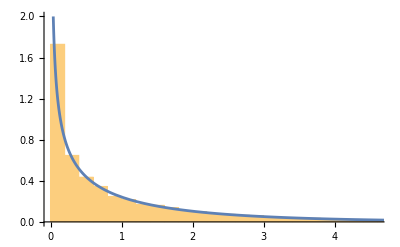

```mathematica
tmp = Block[{sigma = 2},
   dist = TransformedDistribution[Simplify[(n - p)  s2/sigma^2], ndists];
   RandomVariate[dist, 10000]];
cdist = ChiSquareDistribution[n - p];
Show[Histogram[tmp, Automatic, "PDF"],
 Plot[PDF[cdist][x], {x, 0, 5}, PlotRange -> {0, 2}]]
```

```mathematica
uh := Transpose[A] . betah
M := Transpose[A] . Inverse[Transpose[X] . X] . A
r := MatrixRank[A]
F := (uh - u) . Inverse[M] . (uh - u)/r/s2
fdist := FRatioDistribution[r, n - p]
pvalue := 1 - CDF[fdist, F]

Y := y (* この先，実現値のみを扱う．*)
A = Transpose[{{0, 1, 0}, {0, 0, 1}}]; u = {0, 0};
{F, pvalue} // N
```

{0.25,0.816497}

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 3. | 3. | 1. | 0.5
x_1 | -4. | 7.68115 | -0.520756 | 0.69435
x_2 | 2. | 3.31662 | 0.603023 | 0.654545

```mathematica
u = {0};
A = Transpose[{{1, 0, 0}}]; pvalue // N (* k = 0 *)
A = Transpose[{{0, 1, 0}}]; pvalue // N (* k = 1 *)
A = Transpose[{{0, 0, 1}}]; pvalue // N (* k = 2 *)
```

0.5

0.69435

0.654545

```mathematica
s := Sqrt[s2 Diagonal[Inverse[Transpose[X] . X]]]
s // N
```

{3.,7.68115,3.31662}

```mathematica
t := betah/s
t // N
```

{1.,-0.520756,0.603023}

```mathematica
tdist := StudentTDistribution[n - p]
Table[2 Min[CDF[tdist][v], 1 - CDF[tdist][v]], {v, t}] // N
```

{0.5,0.69435,0.654545}

```mathematica
data = Transpose[{{35, 45, 55, 65, 75}, {114, 124, 143, 158, 166}}];
alpha = 5/100; level := ConfidenceLevel -> 1 - alpha
model["ParameterConfidenceIntervalTable", level]
```

| Estimate | Standard Error | Confidence Interval
1 | 65.1 | 5.82838 | {46.5515,83.6485}
x_1 | 1.38 | 0.102632 | {1.05338,1.70662}

```mathematica
tmp = InverseCDF[tdist, 1 - alpha/2];
{betah - s tmp, betah + s tmp} // Transpose // N
```

{{46.5515,83.6485},{1.05338,1.70662}}

```mathematica
cond := F <= InverseCDF[fdist, 1 - alpha]
confint := Reduce[cond]
A = Transpose[{{1, 0}}]; u = {beta0}; confint // N (* k = 0 *)
A = Transpose[{{0, 1}}]; u = {beta1}; confint // N (* k = 1 *)
```

46.5515≤beta0≤83.6485

1.05338≤beta1≤1.70662

```mathematica
tmp = model["ParameterConfidenceIntervals", level];
g1 = Graphics[{Gray, Apply[Rectangle, Transpose[tmp]]}];
g2 = Graphics[model["ParameterConfidenceRegion", level]];
Show[g1, g2, AspectRatio -> 1, Frame -> True]
```

-Graphics-

```mathematica
A = {{1, 0}, {0, 1}}; u = {beta0, beta1};
g3 = RegionPlot[ImplicitRegion[N[cond], Evaluate[u]]];
Show[g1, g3, AspectRatio -> 1, Frame -> True]
```

-Graphics-

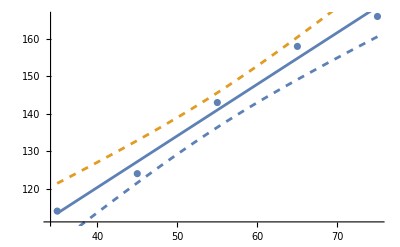

```mathematica
data = Transpose[{{35, 45, 55, 65, 75}, {114, 124, 143, 158, 166}}];
g = Show[ListPlot[data], Plot[model[x1], {x1, 35, 75}],
  Plot[Evaluate[model["MeanPredictionBands", level]],
   Evaluate[{vars[[1]], 35, 75}], PlotStyle -> Dashed]]
```

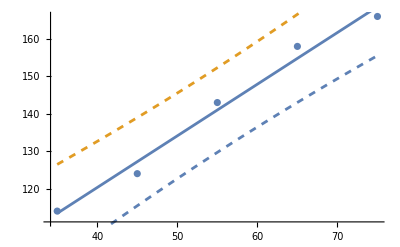

```mathematica
Show[ListPlot[data], Plot[model[x1], {x1, 35, 75}],
   Plot[Evaluate[model["SinglePredictionBands", level]],
     Evaluate[{vars[[1]], 35, 75}], PlotStyle -> Dashed]]
```

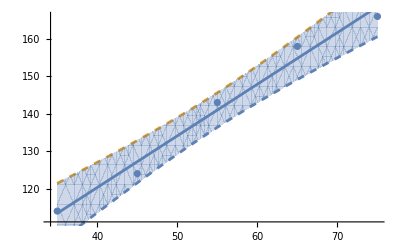

```mathematica
A = {{1}, {vars[[1]]}}; u = {Yp};
Show[g, RegionPlot[Evaluate[cond],
  Evaluate[{vars[[1]], 35, 75}], {Yp, 0, 200}, BoundaryStyle -> None]]
```

## 12 関数の極限と連続性

```mathematica
Clear["Global`*"];
```

```mathematica
f[x_] := 2 x - 3
Limit[f[x], x -> 1]
```

-1

```mathematica
Limit[2 x - 3, x -> 1]
```

-1

```mathematica
f[x_] := Piecewise[{{x^2, x != 2}, {3, x == 2}}]
Limit[f[x], x -> 2]
```

4

```mathematica
g[x_] := (x^2 - 2)/(x - Sqrt[2])
Limit[g[x], x -> Sqrt[2]]
```

2 √2

```mathematica
A := ForAll[epsilon, epsilon > 0, Exists[delta, delta > 0, B]];
B := ForAll[x, Element[x, Reals],
  Implies[0 < Norm[x - a] < delta, Norm[f[x] - alpha] < epsilon]]

f[x_] := 2 x - 3; a = 1; alpha = -1;
Reduce[A, Reals]
```

True

```mathematica
Simplify[Reduce[B, Reals], epsilon > 0]
```

2 delta≤epsilon

```mathematica
Clear[alpha];
Reduce[A, Reals]
```

alpha==-1

```mathematica
Limit[(1 + 1/x)^x, x -> Infinity]
```

ⅇ

```mathematica
Limit[1/x^2, x -> 0]
```

∞

```mathematica
{Limit[RealAbs[x]/x, x -> 0, Direction -> "FromAbove"],
 Limit[RealAbs[x]/x, x -> 0, Direction -> "FromBelow"]}
```

{1,-1}

```mathematica
Clear["Global`*"];
```

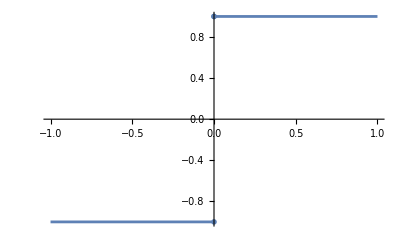

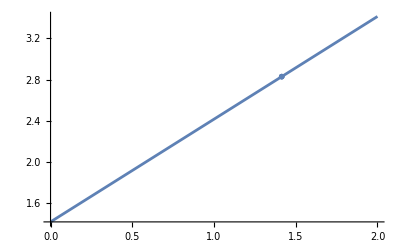

```mathematica
Clear[f, g, x];
f[x_] := Piecewise[{{RealAbs[x]/x, x != 0}}, Undefined]
g[x_] := Piecewise[{{(x^2 - 2)/(x - Sqrt[2]), x != Sqrt[2]}}, Undefined]

ResourceFunction["EnhancedPlot"][f[x], {x, -1, 1}, "FindExceptions" -> True]
ResourceFunction["EnhancedPlot"][g[x], {x, 0, 2},  "FindExceptions" -> True]
```

```mathematica
FunctionContinuous[{f[x], x != 0}, x]
FunctionContinuous[{g[x], x != Sqrt[2]}, x]
```

True

True

## 13 微分

```mathematica
Clear["Global`*"];
```

```mathematica
f[x_] := x^3
f'[1]
```

3

```mathematica
a = 1;
Limit[(f[a + h] - f[a])/h, h -> 0]
```

3

```mathematica
f[x_] := x^3
f'[x]
```

3 x^2

```mathematica
f[x_] := x^3
f1 = f'          (* 方法1 *)
Derivative[1][f] (* 方法2 *)
f2 = f'[x]       (* 方法1 *)
D[f[x], x]       (* 方法2 *)
```

3 #1^2&

3 #1^2&

3 x^2

3 x^2

```mathematica
{f1[1], f2 /. x -> 1}
```

{3,3}

```mathematica
D[x^3, {x, 2}]
```

6 x

```mathematica
Clear[a, b, f, g];
f[t_] := t^2
g[x_] := a x + b
Composition[f, g]'[x]                (* ① *)
D[f[g[x]], x]                        (* ② *)
(D[f[t], t] /. t -> g[x]) D[g[x], x] (* ③ *)
f'[g[x]] g'[x]                       (* ④ *)
```

2 a (b+a x)

2 a (b+a x)

2 a (b+a x)

«1 more identical outputs»

```mathematica
Clear["Global`*"];
```

```mathematica
tmp = Series[Sin[x], {x, 0, 5}]
```

x-x^3/6+x^5/120+O[x]^6

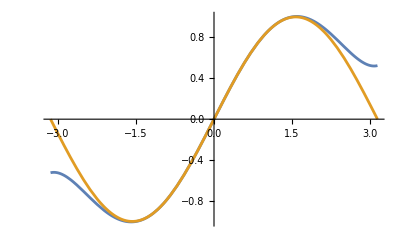

```mathematica
Plot[Evaluate[{Normal[tmp], Sin[x]}], {x, -Pi, Pi}]
```

```mathematica
a = 0; Sum[Derivative[k][Sin][a] (x - a)^k/k!, {k, 0, 5}]
```

x-x^3/6+x^5/120

```mathematica
f[x_] := Sqrt[1 + x]
Series[f[x], {x, 0, 7}]
```

1+x/2-x^2/8+x^3/16-(5 x^4)/128+(7 x^5)/256-(21 x^6)/1024+(33 x^7)/2048+O[x]^8

```mathematica
fn[n_, a_, x_] := Sum[Derivative[k][f][a] (x - a)^k/k!, {k, 0, n},
  GenerateConditions -> True]
Reduce[f[x] == fn[Infinity, 0, x], Reals]
```

-1≤x≤1

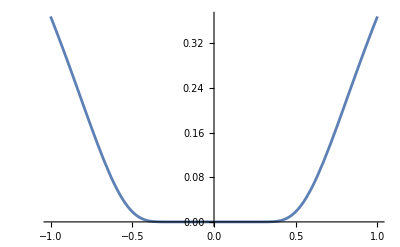

x==0

```mathematica
f[x_] := Piecewise[{{Exp[-1/x^2], x != 0}}, 0]
Plot[f[x], {x, -1, 1}]
Reduce[f[x] == fn[Infinity, 0, x], Reals]
```

```mathematica
Derivative[k][f][0]
```

0

```mathematica
f[x_] := x^3 - 12 x
ResourceFunction["LocalExtrema"][f[x], x]
```

<|Minima→{{-16,{x→2}}},Maxima→{{16,{x→-2}}}|>

```mathematica
sol = SolveValues[f'[x] == 0, x]
Series[f[x], {x, sol[[1]], 2}]
```

{-2,2}

16-6 (x+2)^2+O[x+2]^3

```mathematica
Clear[a, delta];
f[x_] := Piecewise[{{Exp[-1/x^2], x != 0}}, 0]
Reduce[Exists[delta, delta > 0, ForAll[x, Element[x, Reals],
   Implies[0 < Norm[x - a] < delta, f[a] < f[x]]]], Reals]
```

a==0

## 14 積分

```mathematica
Clear["Global`*"];
```

```mathematica
Integrate[-x^2 + 4 x + 1, {x, 1, 4}]
```

12

```mathematica
f[x_] := -x^2 + 4 x + 1
Clear[x]; a = 1; b = 4; h = (b - a)/n;
s = Sum[f[a + k h] h, {k, 1, n}] // Expand
Limit[s, n -> Infinity]
```

12-9/(2 n^2)-9/(2 n)

12

```mathematica
Clear["Global`*"];
```

```mathematica
Integrate[-t^2 + 4 t + 1, {t, a, x}]
```

-a+a^3/3+x-x^3/3+4 (-a^2/2+x^2/2)

```mathematica
Integrate[-x^2 + 4 x + 1, x]
```

x+2 x^2-x^3/3

```mathematica
Clear[x, y];
DSolveValue[y'[x] == -x^2 + 4 x + 1, y[x], x]
```

x+2 x^2-x^3/3+C[1]

```mathematica
DSolveValue[{y'[x] == -x^2 + 4 x + 1, y[0] == 1}, y[x], x]
```

1/3 (3+3 x+6 x^2-x^3)

```mathematica
tmp = DSolveValue[y'[x] == -x y[x], y[x], x]
```

ⅇ^(-x^2/2) C[1]

```mathematica
Reduce[Integrate[tmp, {x, -Infinity, Infinity}] == 1]
```

C[1]==1/(√(2 π))

```mathematica
Clear[a, f, t, x];
Function[x, Evaluate[Integrate[f[t], {t, a, x}]]]'
```

Function[x,f[x]]

```mathematica
D[Integrate[f[t], {t, a, x}], x]
```

f[x]

```mathematica
F = Integrate[-x^2 + 4 x + 1, x];
(F /. x -> 4) - (F /. x -> 1)
```

12

```mathematica
Integrate[Log[Sin[x]], {x, 0, Pi/2}]
```

-1/2 π Log[2]

```mathematica
f[x_] := 1/(2 + Cos[x])
F1x = Integrate[f[x], x];
(F1x /. x -> 2 Pi) - (F1x /. x -> 0) (* 不正解 *)
```

0

```mathematica
F2x = Integrate[f[t], {t, 0, x}, GenerateConditions -> True];
(F2x /. x -> 2 Pi) - (F2x /. x -> 0) (* 正解 *)
```

(2 π)/(√3)

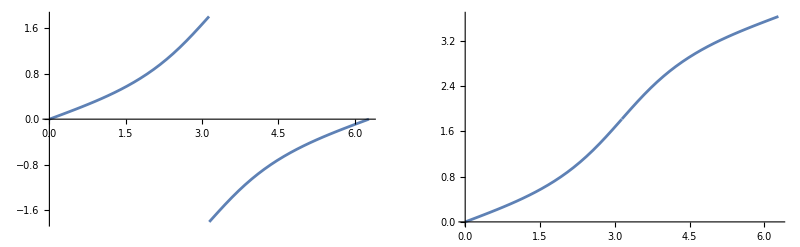

```mathematica
GraphicsRow[{Plot[F1x, {x, 0, 2 Pi}], Plot[F2x, {x, 0, 2 Pi}]}]
```

```mathematica
Clear["Global`*"];
```

```mathematica
Integrate[(p x + q)^100, x]
```

(q+p x)^101/(101 p)

```mathematica
tmp = IntegrateChangeVariables[
  Inactive[Integrate][(p x + q)^100, x], u, u == p x + q]
Activate[tmp] /. u -> p x + q
```

u^100/pu

(q+p x)^101/(101 p)

```mathematica
Clear[x, y];
IntegrateChangeVariables[
 Inactive[Integrate][1, {x, 0, t}], y, x == Sqrt[y]]
```

ConditionalExpression[1/(2 √y)y0t^2, t>0]

```mathematica
Clear["Global`*"];
```

```mathematica
Integrate[1/x^a, {x, 0, 1}]
```

ConditionalExpression[1/(1-a), Re[a]<1]

```mathematica
Integrate[1/x^a, {x, 1, Infinity}]
```

ConditionalExpression[1/(-1+a), Re[a]>1]

```mathematica
Integrate[Exp[-x^2], {x, -Infinity, Infinity}]
```

√π

## 15 多変数関数の微分積分

```mathematica
Clear["Global`*"];
```

```mathematica
x = {x1, x2}; f[{x1_, x2_}] := x1 x2^2/(x1^2 + x2^2)
Limit[f[x], x -> {0, 0}]
```

0

```mathematica
A := ForAll[epsilon, epsilon > 0, Exists[delta, delta > 0, B]];
B := ForAll[Evaluate[x], Element[x, Reals],
  Implies[0 < Norm[x - a] < delta, Norm[f[x] - alpha] < epsilon]]
```

```mathematica
a = {0, 0}; alpha = 0;
Reduce[A, Reals]
```

True

```mathematica
Clear[alpha];
Reduce[A, Reals]
```

alpha==0

```mathematica
Clear[x, y]; f[x_, y_] := x^2 y/(x^4 + y^2)
Limit[f[x, y], {x, y} -> {0, 0}]
```

Indeterminate

```mathematica
Clear[x, y, r, theta];
{Limit[Limit[f[x, y], x -> 0], y -> 0],        (* ① *)
 Limit[Limit[f[x, y], y -> 0], x -> 0],        (* ② *)
 Limit[f[r Cos[theta], r Sin[theta]], r -> 0], (* ③ *)
 Limit[f[x, x^2], x -> 0]}                     (* ④ *)
```

{0,0,0,1/2}

```mathematica
f[{x1_, x2_}] := Piecewise[{{0, x1 == x2 == 0}}, x1 x2^2/(x1^2 + x2^2)]
x = {x1, x2};
FunctionContinuous[f[x], x]           (* 方法1 *)
Limit[f[x], x -> {0, 0}] == f[{0, 0}] (* 方法2 *)
```

True

True

```mathematica
f[x_, y_] := Piecewise[{{0, x == y == 0}}, x^2 y/(x^4 + y^2)]
Clear[x, y]; FunctionContinuous[f[x, y], {x, y}]
```

False

```mathematica
Clear["Global`*"];
```

```mathematica
f[x_, y_] := 2 - x^2 - y^2
{D[f[x, y], x], D[f[x, y], y]}
```

{-2 x,-2 y}

```mathematica
f[x_, y_] := 2 - x^2 - y^2
{Derivative[1, 0][f], Derivative[0, 1][f]}
```

{-2 #1&,-2 #2&}

```mathematica
g[{x1_, x2_}] := 2 - x1^2 - x2^2
{Derivative[{1, 0}][g], Derivative[{0, 1}][g]}
```

{-2 #1⟦1⟧&,-2 #1⟦2⟧&}

```mathematica
D[f[x, y], {{x, y}}]  (* 方法1 *)
Grad[f[x, y], {x, y}] (* 方法2 *)
```

{-2 x,-2 y}

{-2 x,-2 y}

```mathematica
f[x_, y_] := 2 x^3 + 5 x y + 2 y^2
D[f[x, y], {{x, y}, 2}] // MatrixForm
```

(12 x | 5
5 | 4)

```mathematica
Clear[f, F];
f[{x1_, x2_}] := Sqrt[x1^2 + x2^2]
x = {x1, x2}; a = {1, 1}; h = x - a;
F[t_] := f[a + t h]
expr := Normal[Series[F[t], {t, 0, 2}]] /. t -> 1
expr // Simplify
```

(x1^2-2 x1 (-2+x2)+x2 (4+x2))/(4 √2)

```mathematica
Block[{h = {h1, h2}}, expr /. Thread[h -> Map[HoldForm, x - a]]]
```

√2+((-1+x1)+(-1+x2))/(√2)+((-1+x1)^2-2 (-1+x1) (-1+x2)+(-1+x2)^2)/(4 √2)

```mathematica
gradf = D[f[x], {x}] /. Thread[x -> a];
H = D[f[x], {x, 2}] /. Thread[x -> a];
f[a] + gradf . (x - a) + (x - a) . H . (x - a)/2 // Simplify
```

(x1^2-2 x1 (-2+x2)+x2 (4+x2))/(4 √2)

```mathematica
x = {x1, x2}; f[{x1_, x2_}] := 2 x1^3 + x1 x2^2 + 5 x1^2 + x2^2
ResourceFunction["LocalExtrema"][f[x], x]
```

<|Minima→{{0,{x1→0,x2→0}}},Maxima→{{125/27,{x1→-5/3,x2→0}}}|>

```mathematica
points := Solve[D[f[x], {x}] == 0 x, x, Reals]; (* 停留点 *)
H := D[f[x], {x, 2}];                           (* ヘッセ行列 *)
Table[With[{h = H /. p},                        (* 停留点でのヘッセ行列 *)
  {p, f[x] /. p, Which[
    PositiveDefiniteMatrixQ[h], -1,             (* 極小 *)
    NegativeDefiniteMatrixQ[h], 1,              (* 極大 *)
    IndefiniteMatrixQ[h], 0,                    (* 極値ではない *)
    True, Null]}],                              (* 不明 *)
 {p, points}]
```

{{{x1→-5/3,x2→0},125/27,1},{{x1→-1,x2→-2},3,0},{{x1→-1,x2→2},3,0},{{x1→0,x2→0},0,-1}}

```mathematica
x = {x1, x2}; f[{x1_, x2_}] := x1^2 + x2^4
PositiveDefiniteMatrixQ[H /. Thread[x -> {0, 0}]] (* False *)
ResourceFunction["LocalExtrema"][f[x], x]
```

False

<|Minima→{{0,{x1→0,x2→0}}},Maxima→{}|>

```mathematica
Clear["Global`*"];
```

```mathematica
d = ImplicitRegion[And[0 <= x <= 1, 0 <= y <= x], {x, y}];
f[x_, y_] := x^2 + y^2
Integrate[f[x, y], Element[{x, y}, d]]
```

1/3

```mathematica
Integrate[Integrate[f[x, y], {y, 0, x}], {x, 0, 1}]
```

1/3

```mathematica
Integrate[Integrate[f[x, y], {x, y, 1}], {y, 0, 1}]
```

1/3

```mathematica
Clear[u, v, x, y];
lhs = Inactive[Integrate][f[x, y], Element[{x, y}, d]]
rhs = IntegrateChangeVariables[lhs, {u, v}, {x == 2 u, y == 3 v}]
{Activate[lhs], Activate[rhs]}
```

(x^2+y^2){x,y}∈ImplicitRegion[0≤x≤1&&0≤y≤x,{x,y}]

6 (4 u^2+9 v^2)u01/2v0(2 u)/3

{1/3,1/3}

```mathematica
f[x_, y_] := x^2 + y^2
{x, y} = {2 u, 3 v};
J = D[{x, y}, {{u, v}}];
detJ = Det[J]
Integrate[Integrate[f[x, y] Abs[detJ], {v, 0, 2 u/3}], {u, 0, 1/2}]
```

6

1/3

```mathematica
{x, y} = {r Cos[theta], r Sin[theta]};
J = D[{x, y}, {{r, theta}}];
Det[J] // Simplify
```

r

```mathematica
Clear[x, y];
lhs = Inactive[Integrate][Exp[-(x^2 + y^2)],
  {y, -Infinity, Infinity}, {x, -Infinity, Infinity}]
rhs = IntegrateChangeVariables[lhs, {r, theta}, "Cartesian" -> "Polar"]
{Activate[lhs], Activate[rhs]}
```

ⅇ^(-x^2-y^2)y-∞∞x-∞∞

ⅇ^(-r^2) rr0∞theta-ππ

{π,π}

## 16 ベクトル

```mathematica
Clear["Global`*"];
```

```mathematica
a = {1/10 + 2/10, 1/10 + 2/10 - 3/10}; b = {3/10, 0};
a == b
```

True

```mathematica
100 {1, 2} + 10 {3, 1}
```

{130,210}

```mathematica
a = {3, 4};
Norm[a]
```

5

```mathematica
Clear[x, y]; a = {x, y}; Sqrt[a . a]
```

√(x^2+y^2)

```mathematica
Simplify[Norm[{x, y}], Element[x | y, Reals]]
```

√(x^2+y^2)

```mathematica
a = {3, 4};
Normalize[a]
```

{3/5,4/5}

```mathematica
a = {1, 0}; b = {1, 1};
ArcCos[a . b/(Norm[a] Norm[b])]
```

π/4

```mathematica
VectorAngle[a, b]
```

π/4

## 17 行列

```mathematica
Clear["Global`*"];
```

```mathematica
MatrixForm[A = {{1, 2, 0}, {0, 3, 4}}]
```

(1 | 2 | 0
0 | 3 | 4)

```mathematica
Clear["Global`*"];
```

```mathematica
x = {5, 7}; DiagonalMatrix[x] // MatrixForm
```

(5 | 0
0 | 7)

```mathematica
SymmetricMatrixQ[{{1, 2}, {2, 3}}]
```

True

```mathematica
Clear["Global`*"];
```

```mathematica
MatrixForm[A = {{11, 12, 13}, {21, 22, 23}, {31, 32, 33}}]
```

(11 | 12 | 13
21 | 22 | 23
31 | 32 | 33)

```mathematica
A[[1 ;; 2, 1 ;; 2]] // MatrixForm
```

(11 | 12
21 | 22)

```mathematica
A[[All, 3]]
```

{13,23,33}

```mathematica
A[[All, {3}]]
```

{{13},{23},{33}}

```mathematica
A[[2, All]] (* 方法1 *)
A[[2]]      (* 方法2 *)
```

{21,22,23}

{21,22,23}

```mathematica
A[[{2}, All]] (* 方法1 *)
A[[{2}]]      (* 方法2 *)
```

{{21,22,23}}

{{21,22,23}}

```mathematica
Clear["Global`*"];
```

```mathematica
10 {{2, 3}, {5, 7}}
```

{{20,30},{50,70}}

```mathematica
{{10, 20}, {30, 40}} + {{2, 3}, {4, 5}}
```

{{12,23},{34,45}}

```mathematica
Clear["Global`*"];
```

```mathematica
A = {{2, 3}, {5, 7}}; B = {{1, 2}, {3, 4}};
A . B
```

{{11,16},{26,38}}

```mathematica
A = {{2, 3}, {5, 7}}; B = {{1, 2, 3}, {4, 5, 6}}; S = A . B;
{p, q} = Dimensions[A]; {r, s} = Dimensions[B];
S1 = Table[Table[A[[i, All]] . B[[All, j]], {j, 1, s}], {i, 1, p}]; (* ① *)
S2 = Sum[A[[All, {j}]] . B[[{j}, All]], {j, 1, q}];                 (* ② *)
S3 = Transpose[Table[A . b, {b, Transpose[B]}]];                    (* ③ *)
S4 = Table[a . B, {a, A}];                                          (* ④ *)
{S == S1, S == S2, S == S3, S == S4}
```

{True,True,True,True}

```mathematica
Clear[a1, a2, x1, x2, p, q, r, s];
x = {x1, x2}; a = {a1, a2};
G = {{p, q}, {q, s}}; A = {{p, q}, {r, s}};
D[a . x, {x}] == a
D[x . G . x, {x}] == 2 G . x // Simplify
D[(A . x) . (A . x), {x}] == 2 Transpose[A] . A . x // Simplify
```

True

True

True

```mathematica
Clear["Global`*"];
```

```mathematica
Det[{{3, 2}, {1, 2}}]
```

4

```mathematica
RegionMeasure[Parallelepiped[{0, 0}, {{3, 1}, {2, 2}}]]
```

4

```mathematica
RegionMeasure[Parallelepiped[{0, 0, 0}, {{2, 1, 0}, {0, 2, 1}, {1, 1, 1}}]]
```

3

```mathematica
Clear["Global`*"];
```

```mathematica
Inverse[{{2, 3}, {5, 7}}]
```

{{-7,3},{5,-2}}

```mathematica
Clear["Global`*"];
```

```mathematica
A = {{3, 2}, {1, 2}}; b = {8, 4};
Inverse[A] . b
```

{2,1}

```mathematica
RowReduce[{{4, 2, 8}, {2, 1, 4}}]
```

{{1,1/2,2},{0,0,0}}

```mathematica
A = {{2, 0, 2}, {0, 2, -2}, {2, 2, 0}};
MatrixRank[A]
```

2

## 18 ベクトル空間

```mathematica
Clear["Global`*"];
```

```mathematica
a1 = {3, 1}; a2 = {2, 2};
ResourceFunction["LinearlyIndependent"][{a1, a2}]
```

True

```mathematica
Reduce[c1 a1 + c2 a2 == {0, 0}]
```

c2==0&&c1==0

```mathematica
Clear["Global`*"];
```

```mathematica
A = {{1, 0, 1}, {1, 1, 0}, {0, 1, -1}};
ResourceFunction["ColumnSpace"][A]["Basis"]
```

{{1,1,0},{0,1,1}}

```mathematica
A = {{1, 0, 1}, {1, 1, 0}, {0, 1, -1}};
tmp = ResourceFunction["ColumnSpace"][A];
Qt = Orthogonalize[tmp["Basis"]]
```

{{1/(√2),1/(√2),0},{-1/(√6),1/(√6),√(2/3)}}

```mathematica
Q = Transpose[Qt];
Qt . Q
```

{{1,0},{0,1}}

```mathematica
A = {{1, 2}, {1, 2}, {0, 0}}; B = {{1, 0}, {1, 1}, {0, 1}};
{tQa, Ra} = QRDecomposition[A]; Qa = Transpose[tQa]; (* 転置が必要 *)
{tQb, Rb} = QRDecomposition[B]; Qb = Transpose[tQb]; (* 転置が必要 *)
{MatrixForm[Qa], MatrixForm[Ra], A == Qa . Ra,
 MatrixForm[Qb], MatrixForm[Rb], B == Qb . Rb}
```

{(1/(√2)
1/(√2)
0),(√2 | 2 √2),True,(1/(√2) | -1/(√6)
1/(√2) | 1/(√6)
0 | √(2/3)),(√2 | 1/(√2)
0 | √(3/2)),True}

```mathematica
qrd[A_] := Module[{m, n, u = Transpose[A], idx = {}, s, Q},
  {m, n} = Dimensions[A];
  Do[Do[u[[i]] = Simplify[u[[i]] - A[[All, i]] . u[[j]] u[[j]]], {j, 1, i - 1}];
   s = Chop[Norm[u[[i]]]];
   If[s != 0, u[[i]] /= s; AppendTo[idx, i]], {i, 1, n}];
  Q = If[Length[idx] != 0, Transpose[u[[idx]]], IdentityMatrix[m]];
  {Q, Transpose[Q] . A}]

A = {{1, 2}, {1, 2}, {0, 0}}; B = {{1, 0}, {1, 1}, {0, 1}};
Map[MatrixForm, qrd[A]] // Simplify (* 動作確認 *)
Map[MatrixForm, qrd[B]] // Simplify (* 動作確認 *)
```

{(1/(√2)
1/(√2)
0),(√2 | 2 √2)}

{(1/(√2) | -1/(√6)
1/(√2) | 1/(√6)
0 | √(2/3)),(√2 | 1/(√2)
0 | √(3/2))}

```mathematica
B = {{1, 0}, {1, 1}, {0, 1}};
{Q, R} = qrd[B];                              (* QR分解 *)
tol = 10^-10;
e = IdentityMatrix[Dimensions[Q][[2]]];
{Chop[N[Transpose[Q] . Q] - e, tol] == 0 e,   (* ① *)
 UpperTriangularMatrixQ[R, Tolerance -> tol], (* ② *)
 Chop[N[B] - Q . R, tol] == 0 B}              (* ③ *)
(* 誤った転置を検出できないから，①でOrthogonalMatrixQは使えない．*)
```

{True,True,True}

```mathematica
Clear["Global`*"];
```

```mathematica
A = {{1, 0}, {1, 1}, {0, 1}};
NullSpace[Transpose[A]]
NullSpace[Transpose[N[A]]] (* 正規直交基底 *)
```

{{1,-1,1}}

{{0.57735,-0.57735,0.57735}}

```mathematica
A = {{1, 0}, {1, 1}, {0, 1}};
basis1 = Orthogonalize[Transpose[A]];            (* 列空間 *)
basis2 = Orthogonalize[NullSpace[Transpose[A]]]; (* 直交補空間 *)
MatrixForm[Q = Transpose[Join[basis1, basis2]]]
Transpose[Q] . Q == IdentityMatrix[3]
```

(1/(√2) | -1/(√6) | 1/(√3)
1/(√2) | 1/(√6) | -1/(√3)
0 | √(2/3) | 1/(√3))

True

```mathematica
A = {{a, b}, {c, d}};
f[x_] := A . x
R = ParametricRegion[{x, y}, {{x, s, s + u}, {y, t, t + u}}];
Rp = TransformedRegion[R, f];
{RegionMeasure[Rp], Abs[Det[A]] u^2}
```

{u^2 Abs[-b c+a d],u^2 Abs[-b c+a d]}

## 19 固有値と固有ベクトル

```mathematica
Clear["Global`*"];
```

```mathematica
A = {{5, 6, 3}, {0, 9, 2}, {0, 6, 8}}; (* 固有ベクトル（絶対値の降順） *)
{vals, vecs} = Eigensystem[N[A]]       (* 近似値：固有ベクトル（正規） *)
{vals, vecs} = Eigensystem[A]          (* 厳密値：固有ベクトル（非正規）*)
```

{{12.,5.,5.},{{0.639602,0.426401,0.639602},{1.,0.,0.},{0.,-0.447214,0.894427}}}

{{12,5,5},{{3,2,3},{0,-1,2},{1,0,0}}}

```mathematica
V = Transpose[vecs]; A . V == V . DiagonalMatrix[vals]
```

True

```mathematica
A = {{5, 6, 3}, {0, 9, 2}, {0, 6, 8}}; n = Length[A];
SolveValues[Det[x IdentityMatrix[n] - A] == 0, x]
```

{5,5,12}

```mathematica
NullSpace[5 IdentityMatrix[n] - A]
```

{{0,-1,2},{1,0,0}}

```mathematica
Clear["Global`*"];
```

```mathematica
S = {{2, 2, -2}, {2, 5, -4}, {-2, -4, 5}};
{Q, L, V} = SingularValueDecomposition[S];
{MatrixForm[Q], MatrixForm[L],
 S == Q . L . Transpose[Q] == V . L . Transpose[V]}
```

{(-1/3 | 2/(√5) | -2/(3 √5)
-2/3 | 0 | (√5)/3
2/3 | 1/(√5) | 4/(3 √5)),(10 | 0 | 0
0 | 1 | 0
0 | 0 | 1),True}

```mathematica
S = {{2, 2, -2}, {2, 5, -4}, {-2, -4, 5}};
{vals, vecs} = Eigensystem[S];           (* ① *)
Q = Transpose[Orthogonalize[vecs]];      (* ②, ③ *)
L = DiagonalMatrix[vals];                (* ④ *)
Chop[N[S] - Q . L . Transpose[Q]] == 0 S (* 近似的な比較 *)
```

True

```mathematica
Clear["Global`*"];
```

```mathematica
PositiveSemidefiniteMatrixQ[{{4, 2}, {2, 1}}]
```

True

```mathematica
A = {{4, 2}, {2, 1}};
AllTrue[Eigenvalues[A], NonNegative]
```

True

```mathematica
x1 = {1, 3, 6, 10}; y = {7, 1, 6, 14}; X = Transpose[{x1, y}];
n = Length[X]; M = ConstantArray[1, {n, n}]/n;
A = X - M . X;
MatrixForm[S = Transpose[A] . A]
v = Eigenvectors[N[S], 1][[1]] (* 最大固有値に対応する固有ベクトル *)
```

(46 | 46
46 | 86)

{0.548304,0.836279}

```mathematica
Reduce[Det[{v, {xp - Mean[x1], yp - Mean[y]}}] == 0, yp] // N
```

yp==-0.626059+1.52521 xp

```mathematica
{U, L, V} = SingularValueDecomposition[A]; (* 特異値分解 *)
V[[All, 1]] // N                           (* Vの第1列（求めるもの）*)
s2 = Diagonal[L]^2;                        (* 特異値の2乗 *)
Accumulate[s2]/Total[s2] // N              (* 累積寄与率（後述）*)
```

{0.548304,0.836279}

{0.879998,1.}

```mathematica
X = N[Transpose[{{1, 3, 6, 10}, {7, 1, 6, 14}}]];
t = Transpose;
MatrixForm[P = PrincipalComponents[X]]                 (* 主成分スコア *)
r = MatrixRank[P]; Pr = P[[All, ;; r]]; tPr = t[Pr];
MatrixForm[tVr1 = Inverse[tPr . Pr] . tPr . X]         (* 主成分（方法1）*)
MatrixForm[tVr2 = (PseudoInverse[P] . X)[[;; r, All]]] (* 主成分（方法2）*)
tVr1[[1]]                        (* 第1主成分（求めるもの）（方法1）*)
tVr2[[1]]                        (* 第1主成分（求めるもの）（方法2）*)
s2 = Diagonal[Transpose[P] . P]; (* 特異値の2乗 *)
Accumulate[s2]/Total[s2]         (* 累積寄与率（後述）*)
```

(2.19321 | 3.34512
6.11428 | -1.61726
0.287976 | -1.38458
-8.59547 | -0.343271)

(-0.548304 | -0.836279
-0.836279 | 0.548304)

(-0.548304 | -0.836279
-0.836279 | 0.548304)

{-0.548304,-0.836279}

{-0.548304,-0.836279}

{0.879998,1.}

## 20 特異値分解と擬似逆行列

```mathematica
Clear["Global`*"];
```

```mathematica
A = {{1, 0}, {1, 1}, {0, 1}};
{U, S, V} = SingularValueDecomposition[A]; tV = Transpose[V];
{Map[MatrixForm, {U, S, tV}], A == U . S . tV}
```

{{(1/(√6) | -1/(√2) | 1/(√3)
√(2/3) | 0 | -1/(√3)
1/(√6) | 1/(√2) | 1/(√3)),(√3 | 0
0 | 1
0 | 0),(1/(√2) | 1/(√2)
-1/(√2) | 1/(√2))},True}

```mathematica
url = "https://github.com/taroyabuki/comath/raw/main/images/boy.jpg";
A = ImageData[ColorConvert[Import[url], "Grayscale"]]; (* 画像の行列への変換 *)
{U, S, V} = SingularValueDecomposition[A];             (* 特異値分解 *)
k = 52;
Ak = U[[All, ;; k]] . S[[;; k, ;; k]] . Transpose[V[[All, ;; k]]]; (* 近似 *)
B = (Ak - Min[Ak])/(Max[Ak] - Min[Ak]); (* 数値を0～1にする．*)
GraphicsRow[{Image[A], Image[B]}]
```

-Graphics-

```mathematica
nonzero[x_, tol_ : 10^-10] := Chop[x, tol] != 0
svd2[A_] := Module[{diag = DiagonalMatrix, eye = IdentityMatrix, t = Transpose,
   gs = Orthogonalize, m, n, G, vals, vecs, s, r, Sr, S, Vr, V, Ur, U},
  {m, n} = Dimensions[A]; G = t[A] . A;                      (* ① *)
  {vals, vecs} = Eigensystem[G];                             (* ② *)
  s = Sqrt[Select[vals, nonzero]]; r = Length[s];            (* ③ *)
  If[r != 0,
   Sr = diag[s, 0, {r, r}];                                  (* ④ *)
   Vr = t[gs[Take[vecs, r]]];                                (* ⑤ *)
   Ur = A . Vr . diag[1/s, 0, {r, r}];                       (* ⑥ *)
   S = diag[s, 0, {m, n}];                                   (* ⑦ *)
   V = If[n == r, Vr, Join[Vr, t[gs[NullSpace[t[Vr]]]], 2]]; (* ⑧ *)
   U = If[m == r, Ur, Join[Ur, t[gs[NullSpace[t[Ur]]]], 2]], (* ⑨ *)
   (* else *)
   S = 0 A; V = eye[n]; U = eye[m];
   Sr = {{0}}; Vr = V[[All, {1}]]; Ur = U[[All, {1}]]];
  {Ur, Sr, Vr, U, S, V}]

A = {{1, 0}, {1, 1}, {0, 1}}; Map[MatrixForm, svd2[A]] (* 動作確認 *)
```

{(1/(√6) | -1/(√2)
√(2/3) | 0
1/(√6) | 1/(√2)),(√3 | 0
0 | 1),(1/(√2) | -1/(√2)
1/(√2) | 1/(√2)),(1/(√6) | -1/(√2) | 1/(√3)
√(2/3) | 0 | -1/(√3)
1/(√6) | 1/(√2) | 1/(√3)),(√3 | 0
0 | 1
0 | 0),(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))}

```mathematica
tol = 10^-10;
isOrtho[A_] := With[{e = IdentityMatrix[Dimensions[A][[2]]]},
  Chop[Transpose[A] . A - e, tol] == 0 e]
isDiagDesc[A_] := With[{d = Diagonal[A]}, d == Sort[Abs[d], Greater]]
t = Transpose;

A = {{1, 0}, {1, 1}, {0, 1}};
{Ur, Sr, Vr, U, S, V} = svd2[A];                   (* 特異値分解 *)
{isOrtho[Ur], isOrtho[Vr], isOrtho[U], isOrtho[V], (* ① *)
 SquareMatrixQ[U], SquareMatrixQ[V],               (* ② *)
 isDiagDesc[Sr], isDiagDesc[S],                    (* ③ *)
 Chop[N[A] - Ur . Sr . t[Vr], tol] == 0 A,         (* ④-1 *)
 Chop[N[A] - U . S . t[V], tol] == 0 A}            (* ④-2 *)
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
Clear["Global`*"];
```

```mathematica
A = {{1, 0}, {1, 1}, {0, 1}}; PseudoInverse[A]
```

{{2/3,1/3,-1/3},{-1/3,1/3,2/3}}

```mathematica
A = {{1, 0}, {1, 1}, {0, 1}}; b = {2, 0, 2};
PseudoInverse[A] . b
```

{2/3,2/3}